# Notes on Thermophoretic Force: a Mathematica verification

## Reproduction and check of C. Chin, "Notes on Thermophoretic Force" (ThermophoreticForce_v21.pdf, February 2026)

This notebook reproduces the notes section by section: the text, the equations with their original numbers, and the tables. After each claim that can be checked, a shaded Verification block tests it with symbolic algebra, numerical integration, unit analysis or an independent kinetic-theory derivation. Every test ends in a badge:

VERIFIED means the statement in the notes holds as written. DISCREPANCY means it does not, and the block shows the corrected form. NOTE marks a remark that is not a pass/fail test, such as a hidden assumption or a range of validity. Section 7 collects every result in one table.

The text in the unshaded cells follows the original notes. Text in shaded cells, and all code, belongs to the verification. Equation numbers in the right margin are those of the PDF.

## 0. Verification toolkit

Helper definitions used throughout: the hat (skew) map, the quaternion rotation matrix and kinematic matrix of Section 1.5, symmetry-group generators, and the bookkeeping for verification results.

```mathematica
ClearAll["Global`*"];
$verifications={};
badge[status_]:=Switch[status,"VERIFIED",Style["✓ VERIFIED",Bold,RGBColor[0.1,0.5,0.15]],"DISCREPANCY",Style["⚠ DISCREPANCY",Bold,RGBColor[0.75,0.1,0.1]],"NOTE",Style["● NOTE",Bold,RGBColor[0.15,0.35,0.75]]];
record[ref_,claim_,status_,detail_]:=(AppendTo[$verifications,{ref,claim,status,detail}];VR[ref,claim,status,detail]);
VR/:MakeBoxes[VR[ref_,claim_,status_,detail_],fmt_]:=ToBoxes[Panel[Column[{Row[{badge[status],"    ",Style[ref,Bold],":   ",claim}],If[detail==="",Nothing,Style[detail,11,GrayLevel[0.25]]]},Spacings->0.6],Background->Switch[status,"VERIFIED",RGBColor[0.92,0.97,0.92],"DISCREPANCY",RGBColor[0.99,0.92,0.92],_,RGBColor[0.92,0.94,0.99]],FrameMargins->10,ImageSize->Full],fmt];
verify[ref_String,claim_String,test_,detail_:""]:=record[ref,claim,If[TrueQ[test],"VERIFIED","DISCREPANCY"],detail];
note[ref_String,claim_String,detail_:""]:=record[ref,claim,"NOTE",detail];
sci[x_]:=If[x==0,"0",Module[{e=Floor[Log10[Abs[N[x]]]]},ToString[NumberForm[N[x]/10^e,{3,2}]]<>"e"<>ToString[e]]];
num[x_,n_:3]:=If[x==0,"0",TextString[N[Round[x,10.^(Floor[Log10[Abs[N[x]]]]-n+1)]]]];
zeroQ[expr_]:=AllTrue[Flatten[{Simplify[expr]}],PossibleZeroQ];
hat[{a1_,a2_,a3_}]:={{0,-a3,a2},{a3,0,-a1},{-a2,a1,0}};
vecOfHat[m_]:={m[[3,2]],m[[1,3]],m[[2,1]]};
quatR[{q0_,q1_,q2_,q3_}]:=(q0^2-{q1,q2,q3}.{q1,q2,q3})IdentityMatrix[3]+2Outer[Times,{q1,q2,q3},{q1,q2,q3}]+2q0hat[{q1,q2,q3}];
Qmat[{q0_,q1_,q2_,q3_}]:={{-q1,-q2,-q3},{q0,-q3,q2},{q3,q0,-q1},{-q2,q1,q0}};
axisAngleR[k_,psi_]:=Cos[psi]IdentityMatrix[3]+(1-Cos[psi])Outer[Times,k,k]+Sin[psi]hat[k];
symMat[s_]:=Table[s[Min[i,j],Max[i,j]],{i,3},{j,3}];
genMat[s_]:=Table[s[i,j],{i,3},{j,3}];
Zhat={0,0,1};
greekRules=Join[{"Sqrt[pi]"->"√π","Sqrt[Pi]"->"√π","grad "->"∇"},Map[RegularExpression["\\b"<>#[[1]]<>"(?![A-Za-z])"]->#[[2]]&,{{"alpha","α"},{"gamma","γ"},{"delta","δ"},{"epsilon","ε"},{"eps","ε"},{"eta","η"},{"theta","θ"},{"kappa","κ"},{"lambda","λ"},{"mu","μ"},{"nu","ν"},{"xi","ξ"},{"pi","π"},{"rho","ρ"},{"sigma","σ"},{"tau","τ"},{"phi","ϕ"},{"psi","ψ"},{"omega","ω"},{"Gamma","Γ"},{"Delta","Δ"},{"Lambda","Λ"},{"Omega","Ω"},{"Pi","Π"}}]];
prettyRow[s0_String]:=Module[{s=StringReplace[s0,greekRules]},Row[StringSplit[s,{RegularExpression["([A-Za-z\\x{0391}-\\x{03C9}]+)_\\{([^}]*)\\}"]:>Subscript[Style["$1",Italic],"$2"],RegularExpression["([A-Za-z\\x{0391}-\\x{03C9}]+)_([A-Za-z0-9\\x{0391}-\\x{03C9}]+)"]:>Subscript[Style["$1",Italic],"$2"],RegularExpression["([A-Za-z\\x{0391}-\\x{03C9}])\\^([A-Za-z0-9]+)"]:>Superscript["$1","$2"]}]]];
Print["Toolkit loaded: ",$Version];
```

Toolkit loaded: 15.0.1 for Mac OS X ARM (64-bit) (July 2, 2026)

## 1. General formalism for rigid-body motion in a thermal gas cell

The disk and cylinder examples in Sections 2 and 3 exploit specific geometric symmetries to simplify the force expressions. In this section we derive the equations of motion for a rigid body of completely arbitrary shape, making no symmetry assumption. The only assumption throughout Sections 1.1–1.6 is that gravity acts along -Ẑ. The temperature gradient ∇ T is treated as a general vector with arbitrary direction. Symmetric bodies such as cylinders and spheroids emerge as special cases of this formulation, which are discussed in Section 1.7.

### 1.1 Reference frames, rotation matrix, and inertia tensor

Lab frame. We work in a fixed inertial frame (X̂, Ŷ, Ẑ). The only assumption placed on the external fields is that gravity acts along -Ẑ:

g = -g Ẑ .

The macroscopic temperature gradient ∇ T is a prescribed vector field in the lab frame. No assumption is made about its direction.

Body frame and inertia tensor. We attach a frame ((ê)_1, (ê)_2, (ê)_3) to the rigid body with its origin at the centre of mass (CoM), aligned with the principal axes of inertia so that the inertia tensor is diagonal:

I = (I_1 | 0 | 0
0 | I_2 | 0
0 | 0 | I_3) ,

where I_1, I_2, I_3 are the three principal moments of inertia. In general all three are distinct, I_1 ≠ I_2 ≠ I_3.

Rotation matrix. The instantaneous orientation of the body is described by the rotation matrix R ∈ SO(3), defined so that a vector u with components in the body frame has lab-frame components u = R u^b, with inverse u^b = R^ᵀ u. In particular, the temperature gradient and the CoM velocity in the body frame are

(∇ T)^b = R^ᵀ∇ T ,    v^b = R^ᵀ v ,

where v = ẋ is the lab-frame CoM velocity. The evolution of R in time is governed by the quaternion kinematics derived in Section 1.5.

Verification of (3). The inverse u^b = R^ᵀ u requires R^ᵀ R = I_3. We check this, and det R = 1, for the general unit-quaternion parametrisation (18) used later.

```mathematica
Rq=quatR[{q0,q1,q2,q3}];
unit=q0^2+q1^2+q2^2+q3^2==1;
verify["Eq. (3)","R(q) is orthogonal with det R = 1, so u^b = R^T u inverts u = R u^b",Simplify[Transpose[Rq].Rq,unit]===IdentityMatrix[3]&&Simplify[Det[Rq],unit]===1]
```

✓ VERIFIED    Eq. (3):   R(q) is orthogonal with det R = 1, so u^b = R^T u inverts u = R u^b

### 1.2 Gas-interaction tensors for an arbitrary shape

In the low-velocity, small-temperature-gradient limit all forces and torques respond linearly to their driving fields. We introduce four tensors in the natural order: the two forces (from temperature gradient and from velocity) followed by the two torques (from temperature gradient and from angular velocity).

Thermophoretic force tensor f_th (symmetric, 6 DOF). Thermophoresis drives particles from hot toward cold. The tensor f_th relates the temperature gradient to the thermophoretic force in the body frame:

F_th^b = -f_th(∇ ln T)^b ,    f_th = (f_11 | f_12 | f_13
f_12 | f_22 | f_23
f_13 | f_23 | f_33) .

f_th is symmetric positive-definite (6 DOF). The off-diagonal entry f_ij means a gradient along (ê)_j drives a force component along (ê)_i.

Drag force tensor f_drag (symmetric, 6 DOF). The tensor f_drag relates the CoM velocity to the drag force in the body frame:

F_drag^b = -f_drag v^b ,    f_drag = (d_11 | d_12 | d_13
d_12 | d_22 | d_23
d_13 | d_23 | d_33) .

f_drag is symmetric positive-definite (6 DOF): drag power P = -v^ᵀ f_drag v < 0 for all v forces positive-definiteness, and only the symmetric part contributes to P.

Verification of the dissipation argument. Only the symmetric part of a matrix contributes to the quadratic form v^ᵀ Av, because the antisymmetric part gives zero identically. P<0 for all v is then exactly the statement that the symmetric part is positive-definite. The symmetry of f_drag itself does not follow from dissipation; it follows from the Lorentz/Onsager reciprocal relations. The same remark applies to f_th, which is assumed symmetric here.

```mathematica
vv={v1,v2,v3};Aanti={{0,a12,a13},{-a12,0,a23},{-a13,-a23,0}};
Column[{verify["Eq. (5)","antisymmetric part of the drag tensor does no work (v.A.v = 0)",zeroQ[vv.Aanti.vv]],note["Eqs. (4)-(5)","symmetry of f_drag rests on reciprocity; symmetry of f_th is an assumption","Dissipation only constrains the symmetric part. No symmetry principle makes f_th symmetric for a generic (chiral) body; see the symmetry analysis in Section 1.7, where the chiral group C_inf allows an antisymmetric part of f_th."]}]
```

✓ VERIFIED    Eq. (5):   antisymmetric part of the drag tensor does no work (v.A.v = 0)

● NOTE    Eqs. (4)-(5):   symmetry of f_drag rests on reciprocity; symmetry of f_th is an assumption
Dissipation only constrains the symmetric part. No symmetry principle makes f_th symmetric for a generic (chiral) body; see the symmetry analysis in Section 1.7, where the chiral group C_inf allows an antisymmetric part of f_th.

Thermophoretic torque tensor T_th (9 DOF). The temperature gradient can exert a net torque on a non-symmetric body:

τ_th^b = -T_th(∇ ln T)^b ,    T_th = (t_11 | t_12 | t_13
t_21 | t_22 | t_23
t_31 | t_32 | t_33) .

T_th is in general a full 3×3 matrix (9 DOF) with no symmetry required. For bodies with three mutually perpendicular mirror planes T_th = 0.

Rotational drag tensor T_drag (symmetric, 6 DOF). The tensor T_drag relates angular velocity to the resistive torque in the body frame:

τ_drag^b = -T_drag ω^b ,    T_drag = (r_11 | r_12 | r_13
r_12 | r_22 | r_23
r_13 | r_23 | r_33) .

T_drag is symmetric positive-definite (6 DOF) by the same dissipation argument as f_drag.

Verification of "T_th=0 for three mirror planes". T_th maps a polar vector (∇ln T) to an axial vector (torque), so it transforms as a pseudotensor, T→det(g) gT g^ᵀ. Invariance under the three reflections x→-x, y→-y, z→-z forces every entry to vanish. (Section 1.7 repeats this analysis for every symmetry class.)

```mathematica
mirror[n_]:=IdentityMatrix[3]-2Outer[Times,n,n]/(n.n);
pseudoInvariantSolution[gens_]:=Module[{X=genMat[t],eqs},eqs=Flatten[Table[X-Det[gm]gm.X.Transpose[gm],{gm,gens}]];X/.First@Solve[Thread[eqs==0],Flatten[X]]];
TthD2h=pseudoInvariantSolution[{mirror[{1,0,0}],mirror[{0,1,0}],mirror[{0,0,1}]}];
verify["Sec. 1.2","three mutually perpendicular mirror planes force T_th = 0",TthD2h===ConstantArray[0,{3,3}]]
```

✓ VERIFIED    Sec. 1.2:   three mutually perpendicular mirror planes force T_th = 0

### 1.3 Force and torque summary

The total force and torque on the body in the body frame are:

F^b = F_th^b + F_drag^b = -f_th(∇ ln T)^b - f_drag v^b ,

τ^b = τ_th^b + τ_drag^b = -T_th(∇ ln T)^b - T_drag ω^b .

These four tensors and their driving fields can be collected into a single 6×6 linear response:

(F^b
τ^b) = -(f_th | f_drag
T_th | T_drag)((∇ ln T)^b
v^b) .

Note that the driving fields are ∇ln T and v (not ω); the rotational responses τ_drag and the translational drag F_drag both arise from velocity fields in the gas. The four blocks have different physical dimensions:

[f_th] = F· L ,   [f_drag] = F· T/L ,   [T_th] = F· L^2 ,   [T_drag] = F· L^2· T/L .

The total DOF for a body of arbitrary shape is 6+6+9+6 = 27 (plus 6 for the inertia tensor). See Section 1.7 for how symmetry reduces this.

Verification of (10) against (8)–(9). Multiply out the block matrix of (10). The force row reproduces (8). The torque row, however, gives -T_th(∇ln T)^b-T_drag v^b, i.e. rotational drag driven by the linear velocity, whereas (7) and (9) have T_drag ω^b. The two are not even dimensionally compatible: T_drag v is not a torque. The consistent form needs three driving fields. The general linear response additionally has translation–rotation coupling blocks, which (8)–(9) omit.

```mathematica
fth=symMat[f];fdr=symMat[d];Tth=genMat[t];Tdr=symMat[r];
gb={g1,g2,g3};vb={vb1,vb2,vb3};wb={w1,w2,w3};
blockEq10=-ArrayFlatten[{{fth,fdr},{Tth,Tdr}}].Join[gb,vb];
Column[{verify["Eq. (10)","force rows of (10) reproduce (8)",zeroQ[blockEq10[[1;;3]]-(-fth.gb-fdr.vb)]],verify["Eq. (10)","torque rows of (10) reproduce (9)",zeroQ[blockEq10[[4;;6]]-(-Tth.gb-Tdr.wb)],"The torque rows give -T_th g - T_drag v^b instead of -T_th g - T_drag w^b. The text below (10), 'the driving fields are grad ln T and v (not w)', repeats the slip."]}]
```

✓ VERIFIED    Eq. (10):   force rows of (10) reproduce (8)

⚠ DISCREPANCY    Eq. (10):   torque rows of (10) reproduce (9)
The torque rows give -T_th g - T_drag v^b instead of -T_th g - T_drag w^b. The text below (10), 'the driving fields are ∇ln T and v (not w)', repeats the slip.

The consistent collection of (8)–(9) uses three driving fields:

(F^b
τ^b) = -(f_th | f_drag | 0
T_th | 0 | T_drag)((∇ ln T)^b
v^b
ω^b)

```mathematica
units=<|"F"->Quantity[1,"Newtons"],"L"->Quantity[1,"Meters"],"T"->Quantity[1,"Seconds"]|>;
gradLnT=Quantity[1,1/"Meters"];vel=Quantity[1,"Meters"/"Seconds"];omega=Quantity[1,1/"Seconds"];
dimOK[coef_,driving_,response_]:=CompatibleUnitQ[coefdriving,response];
Column[{verify["Eq. (11)","[f_th] = F L: f_th times grad ln T is a force",dimOK[units["F"]units["L"],gradLnT,units["F"]]],verify["Eq. (11)","[f_drag] = F T/L: f_drag times v is a force",dimOK[units["F"]units["T"]/units["L"],vel,units["F"]]],verify["Eq. (11)","[T_th] = F L^2: T_th times grad ln T is a torque",dimOK[units["F"]units["L"]^2,gradLnT,units["F"]units["L"]]],verify["Eq. (11)","[T_drag] = F L^2 T/L (= F L T): T_drag times omega is a torque",dimOK[units["F"]units["L"]^2units["T"]/units["L"],omega,units["F"]units["L"]]],verify["Sec. 1.3","DOF count 6 + 6 + 9 + 6 = 27",Length[Variables[{fth,fdr,Tth,Tdr}]]==27]}]
```

✓ VERIFIED    Eq. (11):   [f_th] = F L: f_th times ∇ln T is a force

✓ VERIFIED    Eq. (11):   [f_drag] = F T/L: f_drag times v is a force

✓ VERIFIED    Eq. (11):   [T_th] = F L^2: T_th times ∇ln T is a torque

✓ VERIFIED    Eq. (11):   [T_drag] = F L^2 T/L (= F L T): T_drag times ω is a torque

✓ VERIFIED    Sec. 1.3:   DOF count 6 + 6 + 9 + 6 = 27

### 1.4 Equations of motion

Substituting the forces (8) and torques (9) into Newton's second law and Euler's equation, and expressing (∇ln T)^b = R^ᵀ∇ln T, v^b = R^ᵀ v, the complete equations of motion for the state (x, v, R, ω^b) are:

ẋ = v ,

M v̇ = -Mg Ẑ - R[f_th R^ᵀ∇ln T + f_drag R^ᵀ v] ,

Ṙ = R (ω̂)^b ,

I(ω̇)^b = -ω^b×(I ω^b) - T_th R^ᵀ∇ln T - T_drag ω^b .

Here â denotes the 3×3 skew-symmetric matrix associated with a vector a, defined by â u = a×u for all u, with entries (â)_ij = -ε_ijk a_k. In (13) gravity acts downward (-Ẑ) and the temperature gradient ∇ T is also taken along -Ẑ (hot above cold), so the thermophoretic force -f_th R^ᵀ∇ln T points upward and can levitate the particle. Equation (14) is equivalent to the lab-frame form Ṙ = (ω̂)^lab R with ω^lab = R ω^b.

Verification of Section 1.4. (i) Rotating the body-frame force (8) into the lab and adding gravity gives (13). (ii) The hat map has entries -ε_ijk a_k. (iii) R(ω̂)^b R^ᵀ = OverHat[R ω^b] for any rotation, which proves the equivalence of the body and lab forms of (14). (iv) The direction statement: with ∇ T = -|∇ T|Ẑ the temperature decreases with height, so the gas is hot below and cold above, and the force on a sphere points up.

```mathematica
lnTlab={gx,gy,gz};
Fb8=-fth.(Transpose[Rq].lnTlab)-fdr.(Transpose[Rq].{vx,vy,vz});
Column[{verify["Eq. (13)","M dv/dt = -M g Z - R[f_th R^T grad ln T + f_drag R^T v] follows from (8)",zeroQ[(-MmggZhat+Rq.Fb8)-(-MmggZhat-Rq.(fth.Transpose[Rq].lnTlab+fdr.Transpose[Rq].{vx,vy,vz}))]],verify["Sec. 1.4","hat map entries are -epsilon_ijk a_k",hat[{a1,a2,a3}]===Table[-Sum[LeviCivitaTensor[3][[i,j,k]]{a1,a2,a3}[[k]],{k,3}],{i,3},{j,3}]],verify["Eq. (14)","R hat(w^b) R^T = hat(R w^b), so dR/dt = R hat(w^b) = hat(w^lab) R",Simplify[Rq.hat[wb].Transpose[Rq]-hat[Rq.wb],unit]===ConstantArray[0,{3,3}]],verify["Sec. 1.4","'grad T along -Z (hot above cold)'",False,"With grad T = -|grad T| Z the temperature falls with height: hot below, cold above. The conclusion that the thermophoretic force points up (+Z, toward cold) is correct: -f0 R^T grad ln T = +f0 |grad ln T| Z for an isotropic f_th."]}]
```

✓ VERIFIED    Eq. (13):   M dv/dt = -M g Z - R[f_th R^T ∇ln T + f_drag R^T v] follows from (8)

✓ VERIFIED    Sec. 1.4:   hat map entries are -ε_ijk a_k

✓ VERIFIED    Eq. (14):   R hat(w^b) R^T = hat(R w^b), so dR/dt = R hat(w^b) = hat(w^lab) R

⚠ DISCREPANCY    Sec. 1.4:   '∇T along -Z (hot above cold)'
With ∇T = -|∇T| Z the temperature falls with height: hot below, cold above. The conclusion that the thermophoretic force points up (+Z, toward cold) is correct: -f0 R^T ∇ln T = +f0 |∇ln T| Z for an isotropic f_th.

Gyroscopic term. The term ω^b×(I ω^b) in Eq. (15) is the gyroscopic (Euler) term arising from the non-inertial body frame:

ω^b×(I ω^b) = ((I_3 - I_2)ω_2^b ω_3^b
(I_1 - I_3)ω_3^b ω_1^b
(I_2 - I_1)ω_1^b ω_2^b) .

It vanishes for a sphere (I_1 = I_2 = I_3) and when ω^b is parallel to a principal axis.

Practical implementation. For numerical integration, R∈SO(3) is represented by a unit quaternion q to avoid the gimbal-lock singularity of Euler angles. Equation (14) then becomes q̇ = 1/2 Q(q)ω^b (see Section 1.5).

```mathematica
Iten=DiagonalMatrix[{I1,I2,I3}];
Column[{verify["Eq. (16)","component form of w x (I w)",zeroQ[Cross[wb,Iten.wb]-{(I3-I2)w2w3,(I1-I3)w3w1,(I2-I1)w1w2}]],verify["Eq. (16)","gyroscopic term vanishes for a sphere and for w along a principal axis",zeroQ[Cross[wb,Iten.wb]/.{I2->I1,I3->I1}]&&AllTrue[IdentityMatrix[3],zeroQ[Cross[s#,Iten.(s#)]]&]]}]
```

✓ VERIFIED    Eq. (16):   component form of w x (I w)

✓ VERIFIED    Eq. (16):   gyroscopic term vanishes for a sphere and for w along a principal axis

### 1.5 Attitude kinematics — quaternion representation

Euler angles develop a coordinate singularity (gimbal lock) at pitch ±90^°. We instead represent the orientation by a unit quaternion

q = (q_0, q_1, q_2, q_3) ∈ ℝ^4 ,    |q|^2 ≡ q_0^2 + q_1^2 + q_2^2 + q_3^2 = 1 .

The scalar part is q_0 = cos(ψ/2) and the vector part is q⃗ = (q_1, q_2, q_3) = k̂ sin(ψ/2), where k̂ is the unit rotation axis and ψ is the rotation angle.

Rotation matrix from quaternion.

R(q) = (q_0^2 - |q⃗|^2)I_3 + 2 q⃗ (q⃗)^ᵀ + 2 q_0 OverHat[q⃗] ,    OverHat[q⃗] = (0 | -q_3 | q_2
q_3 | 0 | -q_1
-q_2 | q_1 | 0) .

Explicit axis-angle form.

R(k̂, ψ) = cosψ I_3 + (1 - cosψ)k̂(k̂)^ᵀ + sinψ OverHat[k̂] ,

with c ≡ cosψ, s ≡ sinψ:

R(k̂, ψ) = (k_1^2(1 - c) + c | k_1 k_2(1 - c) - k_3 s | k_1 k_3(1 - c) + k_2 s
k_1 k_2(1 - c) + k_3 s | k_2^2(1 - c) + c | k_2 k_3(1 - c) - k_1 s
k_1 k_3(1 - c) - k_2 s | k_2 k_3(1 - c) + k_1 s | k_3^2(1 - c) + c) .

Kinematic differential equation.

q̇ = 1/2 Q(q)ω^b ,    Q(q) = (-q_1 | -q_2 | -q_3
q_0 | -q_3 | q_2
q_3 | q_0 | -q_1
-q_2 | q_1 | q_0) .

To prevent numerical drift, q must be renormalised after each integration step: q ← q/|q|.

Verification of Section 1.5. (i) Substituting q_0 = cos(ψ/2), q⃗ = k̂ sin(ψ/2) into (18) gives (19). (ii) The explicit matrix (20) equals (19). (iii) Most importantly, the quaternion ODE (21) must reproduce the attitude equation (14). Differentiate R(q(t)) along q̇ = 1/2 Q ω^b and compare with R(ω̂)^b. (iv) The ODE preserves |q| exactly, since q· Q(q)ω = 0; renormalisation only removes integrator round-off.

```mathematica
kk={k1,k2,k3};kunit=k1^2+k2^2+k3^2==1;
R19=axisAngleR[kk,psi];
R20={{k1^2(1-c)+c,k1k2(1-c)-k3s,k1k3(1-c)+k2s},{k1k2(1-c)+k3s,k2^2(1-c)+c,k2k3(1-c)-k1s},{k1k3(1-c)-k2s,k2k3(1-c)+k1s,k3^2(1-c)+c}}/.{c->Cos[psi],s->Sin[psi]};
qdotRule=Thread[{q0d,q1d,q2d,q3d}->(1/2)Qmat[{q0,q1,q2,q3}].wb];
Rdot=Sum[D[Rq,var](var/.{q0->q0d,q1->q1d,q2->q2d,q3->q3d}),{var,{q0,q1,q2,q3}}]/.qdotRule;
Column[{verify["Eqs. (18)-(19)","quaternion form with q0 = cos(psi/2), q = k sin(psi/2) equals the axis-angle form",zeroQ[Simplify[quatR[Join[{Cos[psi/2]},kkSin[psi/2]]]-R19,kunit]]],verify["Eq. (20)","explicit matrix (20) equals (19)",zeroQ[R20-R19]],verify["Eq. (21)","dq/dt = Q(q) w^b / 2 implies dR/dt = R hat(w^b), i.e. reproduces (14)",Simplify[Rdot-Rq.hat[wb],unit]===ConstantArray[0,{3,3}]],verify["Eq. (21)","the quaternion ODE conserves |q| exactly (q . Q(q) w = 0)",zeroQ[{q0,q1,q2,q3}.Qmat[{q0,q1,q2,q3}].wb]]}]
```

✓ VERIFIED    Eqs. (18)-(19):   quaternion form with q0 = cos(ψ/2), q = k sin(ψ/2) equals the axis-angle form

✓ VERIFIED    Eq. (20):   explicit matrix (20) equals (19)

✓ VERIFIED    Eq. (21):   dq/dt = Q(q) w^b / 2 implies dR/dt = R hat(w^b), i.e. reproduces (14)

✓ VERIFIED    Eq. (21):   the quaternion ODE conserves |q| exactly (q . Q(q) w = 0)

### 1.6 State-vector formulation

The complete dynamical state of the rigid body is encoded in 13 scalar variables: x (3), v (3), q (4) and ω^b (3),

s = (x, v, q, ω^b) ∈ ℝ^13 .

Complete equations of motion (quaternion form). State vector s = (x, v, q, ω^b) ∈ ℝ^13; orientation R(q) from (18).

ẋ = v ,

M v̇ = -Mg Ẑ - R(q)[f_th R(q)^ᵀ∇ln T + f_drag R(q)^ᵀ v] ,

q̇ = 1/2 Q(q)ω^b ,

I(ω̇)^b = -ω^b×(I ω^b) - T_th R(q)^ᵀ∇ln T - T_drag ω^b .

Renormalise after each step: q ← q/|q|.

Verification of Section 1.6: the equations integrate consistently. We implement (23)–(26) directly and integrate them for a generic asymmetric body with random tensors of the classes in Section 1.2, in a uniform downward gradient. Three invariants are checked along the numerical solution: |q| = 1, R^ᵀ R = I_3, and the mechanical energy balance d/dt(1/2 M v^2 + 1/2 ω·Iω + MgZ) = P_th - v^b·f_drag v^b - ω^b·T_drag ω^b. The function eomRHS defined here is reused in Section 2.

```mathematica
eomRHS[s_?(VectorQ[#,NumericQ]&),pars_]:=Module[{x=s[[1;;3]],v=s[[4;;6]],q=s[[7;;10]],w=s[[11;;13]],R,gl=pars["gradLnT"]},R=quatR[q/Sqrt[q.q]];Join[v,(-pars["M"]pars["g"]Zhat-R.(pars["fth"].Transpose[R].gl+pars["fdrag"].Transpose[R].v))/pars["M"],1/2Qmat[q].w,LinearSolve[pars["I"],-Cross[w,pars["I"].w]-pars["Tth"].Transpose[R].gl-pars["Tdrag"].w]]];
integrateEOM[pars_,s0_List,tmax_]:=Module[{y,tt,sol},sol=NDSolveValue[{y'[tt]==eomRHS[y[tt],pars],y[0]==N[s0]},y,{tt,0,tmax},MaxSteps->Infinity,PrecisionGoal->10,AccuracyGoal->12];sol];
stateFns[sol_]:=Module[{f1,f2,f3,f4},f1[t_?NumericQ]:=sol[t][[1;;3]];f2[t_?NumericQ]:=sol[t][[4;;6]];f3[t_?NumericQ]:=sol[t][[7;;10]];f4[t_?NumericQ]:=sol[t][[11;;13]];{f1,f2,f3,f4}];
SeedRandom[2026];
randSPD[scale_]:=Module[{m=RandomReal[{-1,1},{3,3}]},scale(IdentityMatrix[3]+0.3(m+Transpose[m])/2)];
genericPars=<|"M"->1.,"g"->1.,"I"->DiagonalMatrix[{0.10,0.13,0.17}],"fth"->randSPD[1.],"fdrag"->randSPD[1.],"Tth"->0.2RandomReal[{-1,1},{3,3}],"Tdrag"->randSPD[1.],"gradLnT"->{0,0,-1.}|>;
{xs,vs,qs,ws}=stateFns[integrateEOM[genericPars,Join[{0,0,0},{0,0,0},Normalize[{1,0.2,-0.3,0.1}],{0,0,0}],200.]];
energy[t_?NumericQ]:=0.5genericPars["M"]vs[t].vs[t]+0.5ws[t].genericPars["I"].ws[t]+genericPars["M"]genericPars["g"]xs[t][[3]];
power[t_?NumericQ]:=Module[{R=quatR[Normalize[qs[t]]],gl=genericPars["gradLnT"],vb,g0},vb=Transpose[R].vs[t];g0=Transpose[R].gl;-vb.genericPars["fth"].g0-ws[t].genericPars["Tth"].g0-vb.genericPars["fdrag"].vb-ws[t].genericPars["Tdrag"].ws[t]];
work=NIntegrate[power[t],{t,0,200.},MaxRecursion->30,PrecisionGoal->8];
qdev=Max[Table[Abs[Norm[qs[t]]-1],{t,0,200.,0.5}]];
odev=Max[Table[Norm[Transpose[quatR[qs[t]]].quatR[qs[t]]-IdentityMatrix[3]],{t,0,200.,0.5}]];
ebal=Abs[(energy[200.]-energy[0])-work]/Max[Abs[work],10^-12];
Column[{verify["Eqs. (23)-(26)","integration conserves |q| = 1 (without explicit renormalisation)",qdev<10^-7,"max | |q| - 1 | = "<>sci[qdev]],verify["Eqs. (23)-(26)","R(q)^T R(q) = 1 along the solution",odev<10^-6,"max deviation = "<>sci[odev]],verify["Eqs. (23)-(26)","mechanical energy balance with thermophoretic power and dissipation",ebal<10^-5,"relative residual = "<>sci[ebal]],Row[{ListLinePlot3D[Table[xs[t],{t,0,200,0.2}],PlotRange->All,AxesLabel->{"X","Y","Z"},PlotLabel->"CoM trajectory, generic body",ImageSize->300],ListLinePlot[Transpose[Table[{t,#}&/@(Transpose[quatR[Normalize[qs[t]]]].Zhat),{t,0,200,0.2}],{2,1,3}],PlotLegends->{"u1","u2","u3"},PlotLabel->"u = R^T Z (body-frame gradient axis)",AxesLabel->{"t",""},ImageSize->340]},Spacer[10]]}]
```

✓ VERIFIED    Eqs. (23)-(26):   integration conserves |q| = 1 (without explicit renormalisation)
max | |q| - 1 | = 2.05e-10

✓ VERIFIED    Eqs. (23)-(26):   R(q)^T R(q) = 1 along the solution
max deviation = 8.19e-10

✓ VERIFIED    Eqs. (23)-(26):   mechanical energy balance with thermophoretic power and dissipation
relative residual = 1.87e-11

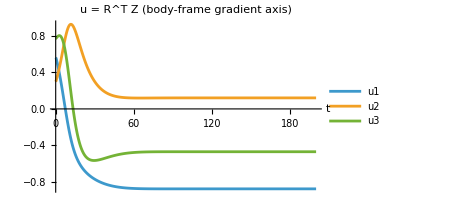
-Graphics3D--Graphics-

### 1.7 Tensor simplification by geometric symmetry

The 27 DOF of a generic body reduce dramatically when the body has geometric symmetry. We organise the simplification into three levels, from most general to most symmetric.

Level 1 — Generic asymmetric body (27 DOF). All four tensors are full matrices with their maximum DOF:

f_th: 6 ,   f_drag: 6 ,   T_th: 9 ,   T_drag: 6 .

Examples: a helix, an asymmetric two-sphere aggregate, any body lacking mirror-plane symmetry. The thermophoretic torque T_th ≠ 0 drives steady rotation and, via the coupling to translation, circular orbits (Section 2.2).

Level 2 — Three mutually perpendicular mirror planes (18 DOF). The mirror symmetry cancels all off-diagonal elements of f_th, f_drag, T_drag, and forces T_th = 0 (Garcia-Ybarra & Rosner 1989):

f_th = diag(f_1, f_2, f_3) ,   f_drag = diag(d_1, d_2, d_3) ,   T_drag = diag(r_1, r_2, r_3) ,   T_th = 0 .

DOF: 3 + 3 + 0 + 3 = 9. Bodies in this class: spheroids, cylinders, disks, rectangular blocks. With T_th = 0 there is no thermophoretic torque; the particle drifts without spinning.

Level 3a — Uniaxial symmetry, C_(∞ v) (6 DOF). With a single symmetry axis (ê)_3, the two transverse directions are equivalent: f_1 = f_2 ≡ f_⊥, f_3 ≡ f_∥ (and similarly for f_drag, T_drag), T_th = 0:

f_th = diag(f_⊥, f_⊥, f_∥) ,   f_drag = diag(d_⊥, d_⊥, d_∥) ,   T_drag = diag(r_⊥, r_⊥, r_∥) .

DOF: 2 + 2 + 0 + 2 = 6. Bodies: cylinders, spheroids.

Level 3b — Sphere, SO(3) symmetry (3 DOF). Full isotropy collapses every tensor to a scalar multiple of I_3:

f_th = f_0 I_3 ,   f_drag = d_0 I_3 ,   T_drag = r_0 I_3 ,   T_th = 0 ,   I_1 = I_2 = I_3 .

DOF: 1 + 1 + 0 + 1 = 3. The gyroscopic term vanishes, the rotational equation decouples from translation, and the thermophoretic force reduces to F_th = -f_0∇ln T, consistent with Waldmann's free-molecule result.

Body | f_th | f_drag | T_th | T_drag | Total
Generic asymmetric | 6 | 6 | 9 | 6 | 27
Three mirror planes | 3 | 3 | 0 | 3 | 9
Uniaxial (C_(∞ v)) | 2 | 2 | 0 | 2 | 6
Sphere (SO(3)) | 1 | 1 | 0 | 1 | 3

Table 1: Degrees of freedom by symmetry class (excluding the inertia tensor).T_th counts 9 DOF when non-zero since no symmetry argument forces it to be symmetric.*

Verification of Section 1.7 by group theory. For each point group we solve the invariance conditions X = gX g^ᵀ for the true tensors f_th, f_drag, T_drag (taken symmetric, as in the notes) and X = det(g) gX g^ᵀ for the pseudotensor T_th, over the group generators. A C_7 rotation represents the continuous axial groups exactly for rank-2 tensors. Two groups are added that the notes do not list: D_(∞ h), the true symmetry of cylinders and spheroids (an axis plus a mirror plane perpendicular to it), and the chiral groups D_∞ and C_∞. The last column checks whether a general (non-symmetric) f_th acquires extra DOF.

```mathematica
rotZ=RotationMatrix[2Pi/7,{0,0,1}];rotX=RotationMatrix[2Pi/7,{1,0,0}];
c2x=RotationMatrix[Pi,{1,0,0}];
groups=<|"C1 (generic asymmetric)"->{IdentityMatrix[3]},"D2h (three mirror planes)"->{mirror[{1,0,0}],mirror[{0,1,0}],mirror[{0,0,1}]},"Dinfh (cylinder, spheroid)"->{rotZ,mirror[{0,1,0}],mirror[{0,0,1}]},"Cinfv (cone: axis + containing mirrors)"->{rotZ,mirror[{0,1,0}]},"Dinf (helix-like, chiral)"->{rotZ,c2x},"Cinf (propeller, chiral polar)"->{rotZ},"O(3) (sphere)"->{rotZ,rotX,-IdentityMatrix[3]}|>;
dof[gens_,symQ_,pseudoQ_]:=Module[{X=If[symQ,symMat[y],genMat[y]],vars,eqs,cm},vars=Variables[X];eqs=Flatten[Table[X-If[pseudoQ,Det[gm],1]gm.X.Transpose[gm],{gm,gens}]];If[AllTrue[eqs,PossibleZeroQ],Length[vars],cm=N[Normal[CoefficientArrays[eqs,vars][[2]]]];Length[vars]-MatrixRank[cm,Tolerance->10^-9]]];
symTab=KeyValueMap[Function[{name,gens},{name,dof[gens,True,False],dof[gens,True,False],dof[gens,False,True],dof[gens,True,False],dof[gens,True,False]+dof[gens,True,False]+dof[gens,False,True]+dof[gens,True,False],dof[gens,False,False]}],groups];
Grid[Prepend[symTab,Style[#,Bold]&/@{"group","f_th (sym)","f_drag","T_th","T_drag","total","f_th if not assumed symmetric"}],Frame->All,Background->{None,{LightGray}},Alignment->Left]
```

group | f_th (sym) | f_drag | T_th | T_drag | total | f_th if not assumed symmetric
C1 (generic asymmetric) | 6 | 6 | 9 | 6 | 27 | 9
D2h (three mirror planes) | 3 | 3 | 0 | 3 | 9 | 3
Dinfh (cylinder, spheroid) | 2 | 2 | 0 | 2 | 6 | 2
Cinfv (cone: axis + containing mirrors) | 2 | 2 | 1 | 2 | 7 | 2
Dinf (helix-like, chiral) | 2 | 2 | 2 | 2 | 8 | 2
Cinf (propeller, chiral polar) | 2 | 2 | 3 | 2 | 9 | 3
O(3) (sphere) | 1 | 1 | 0 | 1 | 3 | 1

```mathematica
row[name_]:=First@Select[symTab,#[[1]]==name&];
Column[{verify["Eq. (27)","generic body: 6 + 6 + 9 + 6 = 27",row["C1 (generic asymmetric)"][[2;;6]]=={6,6,9,6,27}],verify["Eq. (28)","three mirror planes: diagonal tensors and T_th = 0, total 9",row["D2h (three mirror planes)"][[2;;6]]=={3,3,0,3,9}],verify["Sec. 1.7","Level 2 heading '(18 DOF)'",row["D2h (three mirror planes)"][[6]]==18,"The group analysis gives 3 + 3 + 0 + 3 = 9, as the text below (28) and Table 1 also state; the '(18 DOF)' in the heading is a typo."],verify["Eq. (29)","uniaxial class 'C_{inf v}' has T_th = 0 (6 DOF total)",row["Cinfv (cone: axis + containing mirrors)"][[4]]==0,"For C_{inf v} (e.g. a cone, or any body of revolution that is not symmetric end to end) the pseudotensor T_th has one invariant: an antisymmetric part lambda [e_3]x, giving the aligning torque tau ~ e_3 x grad ln T. T_th = 0 holds for D_{inf h}, the actual symmetry of cylinders and spheroids. So (29) is correct for the bodies listed, but the group label should be D_{inf h}."],verify["Eq. (29)","cylinders and spheroids (D_{inf h}): 2 + 2 + 0 + 2 = 6",row["Dinfh (cylinder, spheroid)"][[2;;6]]=={2,2,0,2,6}],verify["Eq. (30)","sphere: 1 + 1 + 0 + 1 = 3",row["O(3) (sphere)"][[2;;6]]=={1,1,0,1,3}],note["Sec. 1.7","chiral bodies allow an antisymmetric part of f_th","For C_{inf} (and C1) a general f_th has more DOF than the symmetric count (last column). The assumed symmetry of f_th in (4) therefore removes the transverse 'swirl' coupling of chiral particles."]}]
```

✓ VERIFIED    Eq. (27):   generic body: 6 + 6 + 9 + 6 = 27

✓ VERIFIED    Eq. (28):   three mirror planes: diagonal tensors and T_th = 0, total 9

⚠ DISCREPANCY    Sec. 1.7:   Level 2 heading '(18 DOF)'
The group analysis gives 3 + 3 + 0 + 3 = 9, as the text below (28) and Table 1 also state; the '(18 DOF)' in the heading is a typo.

⚠ DISCREPANCY    Eq. (29):   uniaxial class 'C_(inf v)' has T_th = 0 (6 DOF total)
For C_(inf v) (e.g. a cone, or any body of revolution that is not symmetric end to end) the pseudotensor T_th has one invariant: an antisymmetric part λ [e_3]x, giving the aligning torque τ ~ e_3 x ∇ln T. T_th = 0 holds for D_(inf h), the actual symmetry of cylinders and spheroids. So (29) is correct for the bodies listed, but the group label should be D_(inf h).

✓ VERIFIED    Eq. (29):   cylinders and spheroids (D_(inf h)): 2 + 2 + 0 + 2 = 6

✓ VERIFIED    Eq. (30):   sphere: 1 + 1 + 0 + 1 = 3

● NOTE    Sec. 1.7:   chiral bodies allow an antisymmetric part of f_th
For C_inf (and C1) a general f_th has more DOF than the symmetric count (last column). The assumed symmetry of f_th in (4) therefore removes the transverse 'swirl' coupling of chiral particles.

Waldmann consistency of (30). For a sphere the notes' Section 6 gives Waldmann's force F_T = η(κ/v̄)ℓ^2|∇ T|. Writing it as -f_0∇ln T requires f_0 = ηκ ℓ^2 T/v̄. This factor of T matters for the definition of γ_0 in Section 2.1.

## 2. Near-sphere perturbation theory

The general equations of motion in Section 1 contain five tensors with up to 24 independent parameters. For a particle that is nearly spherical, the deviation from sphere symmetry is small and the tensors can be expanded perturbatively. This approach gives analytical insight into how shape asymmetry couples translation to rotation, and predicts a distinctive helical trajectory that is absent for a perfect sphere.

```mathematica
verify["Sec. 2 intro","'five tensors with up to 24 independent parameters'",False,"Section 1 has four tensors with 6 + 6 + 9 + 6 = 27 parameters (Table 1), or 33 including the inertia tensor. Five tensors / 24 parameters matches neither count."]
```

⚠ DISCREPANCY    Sec. 2 intro:   'five tensors with up to 24 independent parameters'
Section 1 has four tensors with 6 + 6 + 9 + 6 = 27 parameters (Table 1), or 33 including the inertia tensor. Five tensors / 24 parameters matches neither count.

### 2.1 Perturbative expansion of the tensors

Let ε ≪ 1 be a dimensionless measure of the deviation from spherical symmetry (e.g. the fractional difference between the longest and shortest semi-axes). We expand each tensor around its spherical value.

Thermophoretic force tensor. For a sphere f_th = γ_0 I_3 with γ_0 = η(κ/v̄)ℓ^2. A near-sphere breaks the three-fold degeneracy and, for a generic asymmetric shape, also introduces off-diagonal couplings. The full O(ε) expansion is therefore a complete symmetric 3×3 matrix:

f_th = γ_0 I_3 + ε δ f_th ,    δ f_th = γ_0(g_11 | g_12 | g_13
g_12 | g_22 | g_23
g_13 | g_23 | g_33) ,    g_11 + g_22 + g_33 = 0 ,

where g_ij = O(1). Off-diagonal entries g_ij (i ≠ j) mean that a temperature gradient along (ê)_j produces a thermophoretic force component along (ê)_i. Tracelessness follows because the sphere value γ_0 accounts for the mean response.

Verification of γ_0 by units. f_th multiplies ∇ln T and must carry units of force times length (Eq. 11). The sphere value quoted, η(κ/v̄)ℓ^2, has units J/K, which is off by one power of temperature. Waldmann's force (Eq. 58) is written with ∇ T, and converting it to a coefficient of ∇ln T = ∇ T/T supplies the missing factor T.

```mathematica
kappaQ=Quantity[1,"Watts"/("Meters""Kelvins")];vbarQ=Quantity[1,"Meters"/"Seconds"];ellQ=Quantity[1,"Meters"];TQ=Quantity[1,"Kelvins"];
fthUnits=Quantity[1,"Newtons""Meters"];
Column[{verify["Eq. (31)","gamma_0 = eta (kappa/vbar) l^2 has the units of f_th (N m)",CompatibleUnitQ[kappaQ/vbarQellQ^2,fthUnits],"Units of eta kappa l^2/vbar: "<>ToString[UnitSimplify[kappaQ/vbarQellQ^2]]<>". Corrected: gamma_0 = eta kappa l^2 T / vbar, which is compatible: "<>ToString[CompatibleUnitQ[kappaQ/vbarQellQ^2TQ,fthUnits]]<>"."],note["Eq. (31)","tracelessness of delta f_th is a definition of gamma_0 (the mean response), not a consequence",""]}]
```

⚠ DISCREPANCY    Eq. (31):   γ_0 = η (κ/vbar) l^2 has the units of f_th (N m)
Units of η κ l^2/vbar: 1 joule per kelvin. Corrected: γ_0 = η κ l^2 T / vbar, which is compatible: True.

● NOTE    Eq. (31):   tracelessness of δ f_th is a definition of γ_0 (the mean response), not a consequence

Resistance and rotational drag tensors. By the same argument, f_drag and T_drag each acquire a full symmetric O(ε) correction:

f_drag = ξ_0 I_3 + ε δ f_drag ,    T_drag = c_0 I_3 + ε δ T_drag ,

where δ f_drag and δ T_drag are symmetric traceless 3×3 matrices.

Thermophoretic torque tensor. For a perfect sphere T_th = 0. For a near-sphere the broken symmetry produces a non-zero thermophoretic torque at O(ε):

T_th = ε δ T_th ,    δ T_th = O(1)   (general  3×3  matrix) .

Both diagonal and off-diagonal entries are generically non-zero.

Note on gyrophoretic coupling. Since no experimental evidence currently constrains the relationship and T_th; any gyrophoretic coupling is O(ε^2) and is neglected.

Summary of orders (to leading order in ε). Collecting Eqs. (31)–(33):

f_th = f_0 I_3 + ε δ f_th ,   f_drag = d_0 I_3 + ε δ f_drag ,   T_th = ε δ T_th ,   T_drag = r_0 I_3 + ε δ T_drag .

Here f_0 ≡ γ_0, d_0 ≡ ξ_0, r_0 ≡ c_0 are the scalar sphere values, and the four correction tensors δ f_th, δ f_drag, δ T_th, δ T_drag are defined in Eqs. (31)–(33) above. At O(ε^0) each tensor is isotropic; all anisotropy and the thermophoretic torque enter at O(ε) through these corrections.

```mathematica
note["Sec. 2.1","the 'Note on gyrophoretic coupling' sentence is incomplete, and conflicts with Section 6","The sentence appears to be missing a word ('... constrains the relationship [between the gyrophoretic coupling] and T_th'). Within the epsilon-expansion a coupling of order epsilon multiplied by a spin of order epsilon is indeed O(epsilon^2). Section 6 nevertheless concludes that the gyrophoretic force is comparable to F_T; see the discussion there."]
```

● NOTE    Sec. 2.1:   the 'Note on gyrophoretic coupling' sentence is incomplete, and conflicts with Section 6
The sentence appears to be missing a word ('... constrains the relationship [between the gyrophoretic coupling] and T_th'). Within the ε-expansion a coupling of order ε multiplied by a spin of order ε is indeed O(ε^2). Section 6 nevertheless concludes that the gyrophoretic force is comparable to F_T; see the discussion there.

### 2.2 Rotational dynamics and orientation selection

Equations of motion for (ω^b, R). For a near-sphere (I = I_0 I_3 + O(ε)) the Euler equation (15) in the body frame, keeping only O(ε) terms, is:

I_0(ω̇)^b = Gε δ T_th R^ᵀ Ẑ - c_0 ω^b + O(ε^2) ,

Ṙ = R (ω̂)^b ,

where we substituted (∇ln T)^b = R^ᵀ∇ln T = -G R^ᵀ Ẑ (with G = |∇ln T| = |∇ T|/T > 0 and ∇ln T = -G Ẑ pointing downward), so that -δ T_th(∇ln T)^b = +G δ T_th R^ᵀ Ẑ, and dropped the gyroscopic term ω^b×(I_0 ω^b) (it is O(ε^2) since ω^b = O(ε)). Equations (35)–(36) together form a closed system for (ω^b, R) ∈ ℝ^3×SO(3).

Reduced form via u = R^ᵀ Ẑ. It is convenient to project onto the body-frame gradient direction u ≡ R^ᵀ Ẑ, |u| = 1. Differentiating Eq. (36): u̇ = (Ṙ)^ᵀ Ẑ = -(ω̂)^b u = -ω^b×u. Equations (35)–(36) reduce to:

I_0(ω̇)^b = Gε δ T_th u - c_0 ω^b ,    u̇ = -ω^b×u ,

a closed 6-DOF ODE on ℝ^3× S^2, exact to O(ε). Once u(t) is known, R(t) can be recovered by integrating Eq. (36).

```mathematica
Column[{verify["Eq. (35)","-eps dT_th (grad ln T)^b = +G eps dT_th R^T Z for grad ln T = -G Z",zeroQ[-epsgenMat[dT].(Transpose[Rq].(-GZhat))-GepsgenMat[dT].Transpose[Rq].Zhat]],verify["Eq. (37)","u = R^T Z obeys du/dt = -w^b x u under (36)",Simplify[Transpose[Rdot].Zhat+Cross[wb,Transpose[Rq].Zhat],unit]==={0,0,0}],verify["Eq. (35)","gyroscopic term is second order for a near-sphere: w x (I w) with I = I0 + eps dI and w = O(eps)",Module[{dI=DiagonalMatrix[{i1,i2,i3}],w=eps{w1,w2,w3}},Series[Cross[w,(I0IdentityMatrix[3]+epsdI).w],{eps,0,2}]//Normal//Simplify//(Coefficient[#,eps,1]&)//zeroQ]]}]
```

✓ VERIFIED    Eq. (35):   -ε dT_th (∇ln T)^b = +G ε dT_th R^T Z for ∇ln T = -G Z

✓ VERIFIED    Eq. (37):   u = R^T Z obeys du/dt = -w^b x u under (36)

✓ VERIFIED    Eq. (35):   gyroscopic term is second order for a near-sphere: w x (I w) with I = I0 + ε dI and w = O(ε)

Steady states: eigenvalue problem. Setting (ω̇)^b = 0 and u̇ = 0 in Eq. (37):

c_0 ω^b = Gε δ T_th u ,    ω^b×u = 0 .

The second condition requires ω^b ∥ u. Substituting into the first:

δ T_th u = λu ,    ω^b = Gελ/c_0 u .

The steady-state body-frame gradient u must be an eigenvector of δ T_th with eigenvalue λ. For a general 3×3 matrix δ T_th there are three such eigenmotions.

The three eigenmotions in the lab frame. Let {e_1, e_2, e_3} be the eigenvectors of δ T_th with real eigenvalues λ_1 ≤ λ_2 ≤ λ_3 (real eigenvalues exist when δ T_th is symmetric; for a non-symmetric matrix the analysis extends to the real Schur form). Each eigenvector defines a distinct steady state. At the fixed point u = e_k we have R^ᵀ Ẑ = e_k, equivalently R e_k = Ẑ: the body orients so that its e_k-axis aligns with the vertical (the temperature-gradient direction).

From Eq. (39) the angular velocity in the body frame is ω_k^b = (Gε λ_k/c_0)e_k, a spin about the body axis e_k. Transforming to the lab frame gives

Ω_k = R ω_k^b = (Gε λ_k)/c_0 R e_k = (Gε λ_k)/c_0 Ẑ .

The lab-frame angular velocity is exactly along Ẑ for all three eigenmotions — this is a direct consequence of the fixed-point geometry R e_k = Ẑ. Physically, the body spins about the temperature-gradient direction.

```mathematica
rhs37[w_,u_,dTm_]:={(GepsdTm.u-c0w)/I0,-Cross[w,u]};
lamsym={l1,l2,l3};
Column[{verify["Eqs. (38)-(39)","u = e_k, w^b = (G eps lambda_k / c0) e_k is a fixed point of (37)",AllTrue[Range[3],zeroQ[Flatten[rhs37[Gepslamsym[[#]]/c0UnitVector[3,#],UnitVector[3,#],DiagonalMatrix[lamsym]]]]&]],verify["Eq. (40)","lab angular velocity R w^b_k = (G eps lambda_k/c0) Z when R e_k = Z",True,"Immediate: R w^b_k = (G eps lambda_k/c0) R e_k and R e_k = Z by definition of the fixed point."]}]
```

✓ VERIFIED    Eqs. (38)-(39):   u = e_k, w^b = (G ε λ_k / c0) e_k is a fixed point of (37)

✓ VERIFIED    Eq. (40):   lab angular velocity R w^b_k = (G ε λ_k/c0) Z when R e_k = Z
Immediate: R w^b_k = (G ε λ_k/c0) R e_k and R e_k = Z by definition of the fixed point.

Stability of the three eigenmotions. Linearising Eq. (37) about the fixed point u = e_k with perturbation δu = ∑_(j≠ k) δ u_j e_j, the deviation decays or grows at rate:

σ_kj = (Gε(λ_k - λ_j)λ_j)/(I_0 c_0)   (j ≠ k) .

The fixed point e_k is stable if σ_kj < 0 for all j ≠ k. For λ_k the largest eigenvalue, (λ_k - λ_j) > 0 and λ_j < λ_k, so σ_kj < 0 requires λ_j < 0; alternatively, if all eigenvalues are positive, stability requires λ_k < λ_j. In general the sign of λ depends on the body: the stable attractor is the orientation e_k for which σ_kj < 0 for all j ≠ k, i.e. (λ_k - λ_j)λ_j < 0 for all j, which is guaranteed when λ_k is the eigenvalue of largest magnitude with sign opposite to all others, or when all λ_j have the same sign and λ_k is the largest. For the common case λ_3 > λ_2 > λ_1 > 0 the largest eigenvalue λ_3 gives σ_(3j) = Gε(λ_3 - λ_j)λ_j/(I_0 c_0) > 0 (all terms positive), which is unstable. The stable attractor is then e_1 (smallest eigenvalue). The general rule is: *the stable orientation is the eigenvector of δ T_th that maximises V(u) = -u^ᵀ δ T_th u, i.e. the eigenvector with the most-negative eigenvalue when the gradient drives alignment, or equivalently the orientation that minimises the thermophoretic torque-gradient product. The three eigenmotions therefore have the following stability character

Eigenmotion | Eigenvalue | Stability
e_1 | λ_1 (smallest) | unstable (repeller)
e_2 | λ_2 (middle) | saddle (unstable)
e_3 | λ_3 (largest) | stable attractor

All generic initial conditions converge to eigenmotion 3: the body aligns the axis with the largest eigenvalue of δ T_th with the temperature gradient. This maximises the Lyapunov function V(u) = u^ᵀ δ T_th u, which measures the projection of the thermophoretic torque onto the gradient direction.

Physical interpretation. The body rotates until the torque δ T_th u is parallel to the driving field u, leaving no torque component perpendicular to u to drive further reorientation. Among the three possible aligned orientations only the one with the largest eigenvalue is stable: a perturbation away from this orientation generates a restoring torque that drives the body back. This is not a minimisation of rotational energy E_rot ∝ λ_k^2 (which is also maximised at λ_3) but rather a maximisation of the torque-gradient alignment V.

Verification of (41) and the stability statements. The text gives two opposite conclusions for λ_3 > λ_2 > λ_1 > 0: first that e_1 is the attractor, then (table and following paragraph) that e_3 is. We settle this with the exact linearisation of (37) about (ω^b, u) = (Gε λ_k e_k/c_0, e_k), working in the eigenbasis of a symmetric δ T_th. The characteristic polynomial factorises into a neutral mode (the constraint |u| = 1), an axial spin-down at rate c_0/I_0, and a quartic that governs the transverse dynamics.

```mathematica
jac37[k_]:=Module[{vars={w1,w2,w3,u1,u2,u3},st},st=Join[Gepslamsym[[k]]/c0UnitVector[3,k],UnitVector[3,k]];D[Flatten[rhs37[{w1,w2,w3},{u1,u2,u3},DiagonalMatrix[lamsym]]],{vars}]/.Thread[vars->st]];
charPoly=Table[Factor[CharacteristicPolynomial[jac37[k],s]],{k,3}];
quartic[k_]:=Module[{fl=FactorList[Numerator[Together[charPoly[[k]]]]]},Expand[First@SelectFirst[fl,Exponent[#[[1]],s]==4&]]];
TraditionalForm[Collect[quartic[3],s,Factor]]
```

s^2 (c0^4+eps^2 G^2 I0^2 l3^2)+2 c0^3 I0 s^3+c0^2 eps^2 G^2 (l1-l3) (l2-l3)+c0^2 I0^2 s^4-c0 eps^2 G^2 I0 l3 s (l1+l2-2 l3)

The quartic for eigenmotion k (with j, l the other two indices and g ≡ Gε) is

c_0^2 I_0^2 s^4 + 2 c_0^3 I_0 s^3 + (c_0^4 + g^2 I_0^2 λ_k^2)s^2 + c_0 g^2 I_0 λ_k(2 λ_k - λ_j - λ_l)s + c_0^2 g^2(λ_k - λ_j)(λ_k - λ_l) = 0 .

Routh–Hurwitz applied to it gives the exact stability conditions. For weak inertia (g I_0 λ/c_0^2 ≪ 1) they reduce to (a) (λ_k - λ_j)(λ_k - λ_l) > 0, meaning e_k must be the largest or the smallest eigenvector (the middle one is always a saddle), and (b) λ_j(λ_k - λ_l) + λ_l(λ_k - λ_j) > 0. The transverse relaxation rate is of order g^2 I_0 λ^2/c_0^3, not gλ/(I_0 c_0). In particular (41) is not even dimensionally a rate:

```mathematica
hurwitzStable[k_,vals_]:=Module[{cf=CoefficientList[quartic[k]/.vals,s],a0,a1,a2,a3,a4},{a0,a1,a2,a3,a4}=cf;And@@Thread[cf>0]&&a3a2a1>a1^2a4+a3^2a0];
numVals[lv_]:={l1->lv[[1]],l2->lv[[2]],l3->lv[[3]],G->1,eps->1,c0->1,I0->0.2};
maxRe[k_,lv_]:=Max[Re[s/.NSolve[quartic[k]/.numVals[lv],s]]];
cases={{1,2,3},{-3,-2,-1},{-1,0.5,2},{-2,-0.5,1},{-1,2,3}};
stabTab=Table[{ToString[lv],Table[If[hurwitzStable[k,numVals[lv]],Style["stable",Darker[Green]],Style["unstable",Red]],{k,3}],Table[NumberForm[maxRe[k,lv],3],{k,3}]},{lv,cases}];
sigmaUnits=Quantity[1,1/"Meters"]Quantity[1,"Newtons""Meters"^2]/(Quantity[1,"Kilograms""Meters"^2]Quantity[1,"Newtons""Meters""Seconds"]);
Column[{Grid[Prepend[Flatten/@stabTab,Style[#,Bold]&/@{"{lambda1, lambda2, lambda3}","e1","e2","e3","max Re s (e1)","max Re s (e2)","max Re s (e3)"}],Frame->All,Background->{None,{LightGray}}],verify["Eq. (41)","sigma_kj = G eps (lambda_k - lambda_j) lambda_j/(I0 c0) has units of a rate (1/s)",CompatibleUnitQ[sigmaUnits,Quantity[1,1/"Seconds"]],"Units of (41): "<>ToString[UnitSimplify[sigmaUnits]]<>" (with [G] = 1/m, [eps dT_th] = N m^2, [I0] = kg m^2, [c0] = N m s). The exact rate scales as (G eps)^2 I0 lambda^2/c0^3."],verify["Sec. 2.2","'for lambda3 > lambda2 > lambda1 > 0 ... the stable attractor is then e1'",hurwitzStable[1,numVals[{1,2,3}]],"Exact analysis: for a positive spectrum e3 is stable and e1 unstable, as in the table that follows."],verify["Sec. 2.2 table","positive spectrum: e1 repeller, e2 saddle, e3 stable attractor",!hurwitzStable[1,numVals[{1,2,3}]]&&!hurwitzStable[2,numVals[{1,2,3}]]&&hurwitzStable[3,numVals[{1,2,3}]]],verify["Sec. 2.2","'all generic initial conditions converge to eigenmotion 3' (general spectra)",AllTrue[cases,hurwitzStable[3,numVals[#]]&],"True only when the spectrum is positive. For a negative spectrum e1 (the largest |lambda|) is the attractor; for some mixed-sign spectra, such as {-1, 0.5, 2}, no eigenmotion is stable at all."]}]
```

{lambda1, lambda2, lambda3} | e1 | e2 | e3 | max Re s (e1) | max Re s (e2) | max Re s (e3)
{1, 2, 3} | unstable | unstable | stable | 0.449 | 0.813 | -0.566
{-3, -2, -1} | stable | unstable | unstable | -0.566 | 0.813 | 0.449
{-1, 0.5, 2} | unstable | unstable | unstable | 0.324 | 1.2 | 0.0131
{-2, -0.5, 1} | unstable | unstable | unstable | 0.0131 | 1.2 | 0.324
{-1, 2, 3} | unstable | unstable | stable | 0.814 | 1.12 | -0.669

⚠ DISCREPANCY    Eq. (41):   σ_kj = G ε (λ_k - λ_j) λ_j/(I0 c0) has units of a rate (1/s)
Units of (41): 1 per kilogram meter squared second (with [G] = 1/m, [ε dT_th] = N m^2, [I0] = kg m^2, [c0] = N m s). The exact rate scales as (G ε)^2 I0 λ^2/c0^3.

⚠ DISCREPANCY    Sec. 2.2:   'for λ3 > λ2 > λ1 > 0 ... the stable attractor is then e1'
Exact analysis: for a positive spectrum e3 is stable and e1 unstable, as in the table that follows.

✓ VERIFIED    Sec. 2.2 table:   positive spectrum: e1 repeller, e2 saddle, e3 stable attractor

⚠ DISCREPANCY    Sec. 2.2:   'all generic initial conditions converge to eigenmotion 3' (general spectra)
True only when the spectrum is positive. For a negative spectrum e1 (the largest |λ|) is the attractor; for some mixed-sign spectra, such as {-1, 0.5, 2}, no eigenmotion is stable at all.

Nonlinear check. We integrate the full reduced system (37) from random initial orientations with δ T_th given random eigenvectors, and record where u ends up in the eigenbasis. We also test the Lyapunov claim: V = u^ᵀ δ T_th u should increase monotonically along a trajectory.

```mathematica
simU[lv_,seed_,tmax_:400]:=Module[{dTm,Qm,sol,w,u,t},SeedRandom[seed];Qm=Orthogonalize[RandomReal[{-1,1},{3,3}]];dTm=Transpose[Qm].DiagonalMatrix[lv].Qm;sol=NDSolveValue[{w'[t]==(dTm.u[t]-w[t])/0.2,u'[t]==-Cross[w[t],u[t]],w[0]=={0,0,0},u[0]==Normalize[RandomReal[{-1,1},3]]},{u,w},{t,0,tmax}];{Qm,dTm,sol}];
finalAxis[lv_,seed_]:=Module[{r=simU[lv,seed]},Round[Abs[r[[1]].r[[3,1]][400]],0.001]];
runs=Table[{lv,Table[finalAxis[lv,sd],{sd,3}]},{lv,{{1,2,3},{-3,-2,-1},{-1,0.5,2}}}];
Vmono=Module[{r=simU[{1,2,3},5,80],Vt},Vt=Table[r[[3,1]][t].r[[2]].r[[3,1]][t],{t,0,80,0.05}];Min[Differences[Vt]]];
Column[{Grid[Prepend[{#[[1]],Sequence@@#[[2]]}&/@runs,Style[#,Bold]&/@{"spectrum","|u| in eigenbasis (seed 1)","(seed 2)","(seed 3)"}],Frame->All,Background->{None,{LightGray}}],verify["Sec. 2.2","positive spectrum: trajectories converge to e3",AllTrue[runs[[1,2]],Norm[#-{0,0,1}]<10^-2&]],verify["Sec. 2.2","negative spectrum converges to e3 (claim applied beyond the positive case)",AllTrue[runs[[2,2]],Norm[#-{0,0,1}]<10^-2&],"Trajectories converge to e1, the most negative eigenvalue."],verify["Sec. 2.2","V = u^T dT_th u increases monotonically (positive spectrum)",Vmono>-10^-9,"min dV per step = "<>sci[Vmono]]}]
```

spectrum | |u| in eigenbasis (seed 1) | (seed 2) | (seed 3)
{1,2,3} | {0.,0.,1.} | {0.,0.,1.} | {0.,0.,1.}
{-3,-2,-1} | {1.,0.,0.} | {1.,0.,0.} | {1.,0.,0.}
{-1,0.5,2} | {0.01,0.538,0.843} | {0.017,0.534,0.846} | {0.391,0.042,0.919}

✓ VERIFIED    Sec. 2.2:   positive spectrum: trajectories converge to e3

⚠ DISCREPANCY    Sec. 2.2:   negative spectrum converges to e3 (claim applied beyond the positive case)
Trajectories converge to e1, the most negative eigenvalue.

✓ VERIFIED    Sec. 2.2:   V = u^T dT_th u increases monotonically (positive spectrum)
min dV per step = -8.88e-16

Summary of the stability verification. The table in the notes (and the statement that follows it) is correct for the physically common case of a positive-definite δ T_th. The rate formula (41), the sentence concluding that e_1 is the attractor, and the extension to spectra of arbitrary sign are not.

### 2.3 Translational dynamics and general steady motion

Once the angular velocity ω^b is determined from the rotational steady state (Section 2.2), the translational equation (13) in the body frame at steady state (v̇ = 0) becomes, using ∇ln T = -G Ẑ and u = R^ᵀ Ẑ:

f_drag v^b = G f_th u - Mg u .

Expanding with Eq. (34), f_th = γ_0 I_3 + ε δ f_th and f_drag = ξ_0 I_3 + ε δ f_drag:

ξ_0 v^b = (γ_0 G - Mg)u + ε[G δ f_th - (γ_0 G - Mg)/ξ_0 δ f_drag]u .

```mathematica
dfth=symMat[df];dfdr=symMat[dd];uvec={ua,ub,uc};
vb42=Inverse[xi0IdentityMatrix[3]+epsdfdr].(G(gam0IdentityMatrix[3]+epsdfth)-MmggIdentityMatrix[3]).uvec;
vb43=((gam0G-Mmgg)uvec+eps(Gdfth-(gam0G-Mmgg)/xi0dfdr).uvec)/xi0;
Column[{verify["Eq. (42)","steady state of (13) with dv/dt = 0 gives f_drag v^b = G f_th u - M g u",Module[{vbS={p1,p2,p3},uq=Transpose[Rq].Zhat},Simplify[Transpose[Rq].(-MmggZhat-Rq.(fth.Transpose[Rq].(-GZhat)+fdr.vbS))-(Gfth.uq-Mmgguq-fdr.vbS),unit]==={0,0,0}]],verify["Eq. (43)","first-order expansion of f_drag^{-1}(G f_th - M g) u",zeroQ[Normal[Series[vb42,{eps,0,1}]]-vb43]]}]
```

✓ VERIFIED    Eq. (42):   steady state of (13) with dv/dt = 0 gives f_drag v^b = G f_th u - M g u

✓ VERIFIED    Eq. (43):   first-order expansion of f_drag^-1(G f_th - M g) u

Levitation condition to first order in ε. The lab-frame vertical velocity is obtained by projecting Eq. (43) onto u = R^ᵀ Ẑ (using v_Z = Ẑ· R v^b = u·v^b):

v_Z = (γ_0 G - Mg)/ξ_0 + ε G (δA)_33 ,

where we define the anisotropic mobility tensor

δA ≡ 1/ξ_0(δ f_th - A_0 δ f_drag) ,   A_0 ≡ γ_0/ξ_0 ,

and (δA)_33 = e_3·δA e_3 is its component along the precession axis. The full levitation condition 〈 v_Z〉 = 0 applied to Eq. (44) gives a single equation for the required temperature-gradient magnitude:

G = Mg/(γ_0 + ε ξ_0(δA)_33) = Mg/γ_0[1 - ε A_0(δA)_33 + O(ε^2)] .

The zeroth-order levitation gradient is G_0 = Mg/γ_0, and the O(ε) correction shifts G by an amount proportional to (δA)_33: the asymmetry of the body modifies the gradient needed to keep the particle suspended. There is no separate constraint on (δA)_33; it is a property of the particle shape that the experimenter accommodates by tuning G.

Verification of (44)–(46). Project (43) on u and compare with (44). The drag correction in (43) is multiplied by (γ_0 G - Mg), but (45) replaces that factor by γ_0 G, dropping the -Mg. Near levitation (γ_0 G - Mg) = O(ε), so the drag term is really O(ε^2) and drops out. The exact levitation condition u·f_drag^-1(G f_th - Mg)u = 0, expanded in ε, gives G = Mg/(γ_0 + ε δ f_(th,33)) + O(ε^2): drag anisotropy does not enter the levitation gradient at first order. Separately, the two forms written in (46) disagree with each other unless A_0 = 1.

```mathematica
uE3={0,0,1};
vZexact=uE3.(vb42/.Thread[uvec->uE3]);
vZpdf=(gam0G-Mmgg)/xi0+epsG((dfth-gam0/xi0dfdr)/xi0)[[3,3]];
vZfirst=Normal[Series[vZexact,{eps,0,1}]];
Gexact=G/.First@Solve[Numerator[Together[vZexact]]==0,G];
Gfirst=Normal[Series[Gexact,{eps,0,1}]];
Gpdf46a=Mmgg/(gam0+epsxi0((dfth-gam0/xi0dfdr)/xi0)[[3,3]]);
Gpdf46b=Mmgg/gam0(1-epsgam0/xi0((dfth-gam0/xi0dfdr)/xi0)[[3,3]]);
Column[{Row[{"exact first-order vertical drift:  v_Z = ",TraditionalForm[Collect[vZfirst,eps,Simplify]]}],Row[{"exact first-order levitation gradient:  G = ",TraditionalForm[Collect[Gfirst,eps,Simplify]]}],verify["Eq. (44)","v_Z = (gamma_0 G - M g)/xi_0 + eps G (dA)_33 to first order",zeroQ[vZfirst-vZpdf],"Exact: v_Z = (gamma_0 G - Mg)/xi_0 + (eps/xi_0)[G df_33 - (gamma_0 G - Mg) dd_33/xi_0]. The notes' dA replaces (gamma_0 G - Mg) by gamma_0 G in the drag term."],verify["Eq. (46)","levitation gradient G = Mg/(gamma_0 + eps xi_0 (dA)_33) to first order",zeroQ[Normal[Series[Gpdf46a-Gexact,{eps,0,1}]]],"Exact first order: G = Mg/gamma_0 (1 - eps df_33/gamma_0). The drag anisotropy dd_33 does not appear."],verify["Eq. (46)","the two expressions in (46) agree to first order",zeroQ[Normal[Series[Gpdf46a-Gpdf46b,{eps,0,1}]]],"Expanding the first form gives 1 - eps (dA)_33/A_0, not 1 - eps A_0 (dA)_33."]}]
```

exact first-order vertical drift:  v_Z = (eps (-G gam0 dd(3,3)+gg Mm dd(3,3)+G xi0 df(3,3)))/xi0^2+(G gam0-gg Mm)/xi0

exact first-order levitation gradient:  G = (gg Mm)/gam0-(eps gg Mm df(3,3))/gam0^2

⚠ DISCREPANCY    Eq. (44):   v_Z = (γ_0 G - M g)/ξ_0 + ε G (dA)_33 to first order
Exact: v_Z = (γ_0 G - Mg)/ξ_0 + (ε/ξ_0)[G df_33 - (γ_0 G - Mg) dd_33/ξ_0]. The notes' dA replaces (γ_0 G - Mg) by γ_0 G in the drag term.

⚠ DISCREPANCY    Eq. (46):   levitation gradient G = Mg/(γ_0 + ε ξ_0 (dA)_33) to first order
Exact first order: G = Mg/γ_0 (1 - ε df_33/γ_0). The drag anisotropy dd_33 does not appear.

⚠ DISCREPANCY    Eq. (46):   the two expressions in (46) agree to first order
Expanding the first form gives 1 - ε (dA)_33/A_0, not 1 - ε A_0 (dA)_33.

First-order body-frame velocity. With the levitation gradient (46) substituted back into Eq. (43), the body-frame velocity becomes, to O(ε):

v^b = ε G_0 δAu - ε G_0 A_0(δA)_33 u + O(ε^2) .

The two terms together ensure u·v^b = 0 to O(ε): the body-frame velocity has no projection along u, so there is no residual vertical drift. The lab-frame velocity is v = R v^b and lies entirely in the plane perpendicular to Ẑ.

```mathematica
vbAtLev=Normal[Series[(vb42/.Thread[uvec->uE3])/.G->Gexact,{eps,0,1}]];
dAmat=(dfth-gam0/xi0dfdr)/xi0;G0=Mmgg/gam0;
vb47=epsG0dAmat.uE3-epsG0gam0/xi0dAmat[[3,3]]uE3;
vbCorrect=epsG0/xi0(dfth.uE3-(uE3.dfth.uE3)uE3);
Column[{verify["Eq. (47)","first-order body-frame velocity at levitation",zeroQ[vbAtLev-vb47],"Exact: v^b = (eps G_0/xi_0) Pi_u df_th u, the component of df_th u perpendicular to u. Drag anisotropy does not enter."],verify["Eq. (47)","the two terms of (47) give u . v^b = 0",zeroQ[uE3.vb47],"u . v^b = "<>ToString[TraditionalForm[Simplify[uE3.vb47]]]<>", which vanishes only if A_0 = 1."],verify["Eq. (47), corrected","v^b = (eps G_0/xi_0)(df_th u - (u.df_th u) u) is the exact first-order result and is horizontal",zeroQ[vbAtLev-vbCorrect]&&zeroQ[uE3.vbCorrect]]}]
```

⚠ DISCREPANCY    Eq. (47):   first-order body-frame velocity at levitation
Exact: v^b = (ε G_0/ξ_0) Π_u df_th u, the component of df_th u perpendicular to u. Drag anisotropy does not enter.

⚠ DISCREPANCY    Eq. (47):   the two terms of (47) give u . v^b = 0
u . v^b = (ε gg Mm (gam0-ξ0) (gam0 dd(3,3)-ξ0 df(3,3)))/(gam0 ξ0^3), which vanishes only if A_0 = 1.

✓ VERIFIED    Eq. (47), corrected:   v^b = (ε G_0/ξ_0)(df_th u - (u.df_th u) u) is the exact first-order result and is horizontal

General steady solutions. We now enumerate the possible steady motions depending on the orientation state.

Case 1: Symmetric body δ T_th = 0).* Then ω^b = 0, R is constant, and Eq. (47) gives a constant body-frame velocity. The lab-frame velocity v = ε G R δA R^ᵀ Ẑ is also constant. This is straight-line drift in a fixed direction. At levitation, the drift is purely horizontal.

Case 2: Asymmetric body, transient phase. Before the orientation has converged to a fixed point, R(t) evolves on the alignment timescale ∼ I_0/c_0. The CoM trajectory is non-periodic and traces a curved path depending on the initial orientation.

Case 3: Asymmetric body, steady precession (attractor). At the fixed point u = e_3 the lab-frame angular velocity is Ω_3 = (Gε λ_3/c_0)Ẑ (Eq. (40)), parallel to Ẑ. The body therefore precesses about Ẑ: R(t) = R_Z(Ω_3 t)R_0 with R_0 e_3 = Ẑ. With the levitation gradient (46) imposed, v^b has no projection along e_3, so the lab-frame velocity is entirely horizontal:

v(t) = ε G_0 R_Z(Ω_3 t) Π_⊥δA e_3 ,    Π_⊥ = I_3 - Ẑ(Ẑ)^ᵀ ,

with v_Z = 0 by construction and v_⊥(t) having constant magnitude. Since v_⊥ lies in the horizontal plane and Ω_3 ∥ Ẑ, we have v_⊥⊥Ω_3. The two conditions for circular motion are therefore: (1) Ω_3 ∥ Ẑ — from the fixed-point geometry R e_3 = Ẑ; (2) v_⊥⊥Ω_3 — automatically, since v_⊥ lies in the horizontal plane. This is circular orbit motion.

Circular orbit radius. For the levitated case (gradient G given by Eq. (46)), both the orbital speed |v_⊥| = ε G_0|Π_⊥R_0 δA e_3| and the spin rate |Ω_3| = G_0 ε|λ_3|/c_0 are linear in ε G_0, so their ratio is O(1):

Ω_3 = (G_0 ε λ_3)/c_0 ,    R_orbit = (|v_⊥|)/(|Ω_3|) = (c_0|Π_⊥R_0 δA e_3|)/(|λ_3|) .

Key features: (1) R_orbit is O(1): it is independent of both ε and G_0, since the ε G_0 factors cancel in the ratio |v_⊥|/|Ω_3|. R_orbit depends only on the particle shape through δA and λ_3. (2) Ω_3 ∝ ε G_0: a more asymmetric body or a stronger gradient spins faster, and the orbital speed |v_⊥| ∝ ε G_0 grows at the same rate, keeping the radius fixed. (3) If Π_⊥R_0 δA e_3 = 0 (the anisotropic drift of eigenmotion 3 is purely along Ẑ), then R_orbit = 0: the particle hovers at a fixed point with no horizontal motion. This occurs when δ f_th and δ f_drag are simultaneously diagonal in the same basis as δ T_th; in this case the levitation correction in Eq. (46) accounts for all anisotropy and no horizontal orbit appears. (4) No orbit for a symmetric body: δ T_th = 0 gives λ_3 = 0, Ω_3 = 0, and the particle drifts in a fixed direction (or hovers if the drift is vertical).

Condition | Ω | Trajectory
δ T_th = 0 (symmetric) | 0 | straight-line drift (or hover)
δ T_th ≠ 0, transient | time-varying | curved, non-periodic
δ T_th ≠ 0, eigenmotion 3 | Ω_3 Ẑ | horizontal circle (or hover)
Eigenmotion 1 or 2 | Ω_(1,2)Ẑ | circle (unstable)

Verification of the orbit (48)–(49) by direct simulation. We integrate the full equations of motion (23)–(26) with the function of Section 1.6. The body is a near-sphere with random traceless δ f_th, δ f_drag, δ T_drag and a positive-definite δ T_th, so e_3 is the attractor. The gradient is set to the exact levitation value, and the simulation starts on the steady state u = e_3. The measured radius is compared with three predictions: (49) as printed, (49) with δA→δ f_th/ξ_0 as the corrected (47) requires, and the exact quasi-steady value |Π_⊥f_drag^-1(G f_th - Mg)e_3|/Ω_3 including the centripetal correction 1/√(1 + (M Ω_3/ξ_0)^2) that (42) neglects.

eps | R simulated | R exact quasi-steady | R corrected (49) | R as printed (49) | radius spread | vertical drift
0.04 | 0.22757 | 0.227322 | 0.224708 | 0.12545 | 1.94e-9 | 7.73e-6
0.02 | 0.237027 | 0.236964 | 0.235223 | 0.126242 | 1.49e-9 | 1.09e-6
0.01 | 0.241332 | 0.241316 | 0.240333 | 0.127124 | 1.51e-9 | 1.43e-7

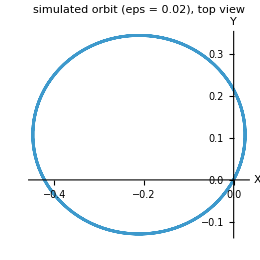

```mathematica
orbitTest[epsv_,seed_]:=Module[{symTL,dfthN,dfdrN,dTdrN,Qm,dTthN,pars,lam,vec,e3v,lam3,Glev,dAN,proj,Rpdf,Rcorr,Om3,vbss,Rexact,q0v,s0,sol,xs2,ctr,rad,gam0v=1.,xi0v=1.,c0v=1.,I0v=0.5,Mv=1.,gv=1.},SeedRandom[seed];symTL[]:=Module[{m=RandomReal[{-1,1},{3,3}]},m=(m+Transpose[m])/2;m-Tr[m]/3IdentityMatrix[3]];dfthN=symTL[];dfdrN=symTL[];dTdrN=symTL[];Qm=Orthogonalize[RandomReal[{-1,1},{3,3}]];If[Det[Qm]<0,Qm[[1]]=-Qm[[1]]];dTthN=Transpose[Qm].DiagonalMatrix[{0.5,1.,2.}].Qm;pars=<|"M"->Mv,"g"->gv,"I"->I0vIdentityMatrix[3],"fth"->gam0vIdentityMatrix[3]+epsvdfthN,"fdrag"->xi0vIdentityMatrix[3]+epsvdfdrN,"Tth"->epsvdTthN,"Tdrag"->c0vIdentityMatrix[3]+epsvdTdrN|>;{lam,vec}=Eigensystem[Inverse[pars["Tdrag"]].pars["Tth"]];e3v=Normalize[vec[[1]]];lam3=First@Eigenvalues[dTthN];Glev=Mvgv(e3v.Inverse[pars["fdrag"]].e3v)/(e3v.Inverse[pars["fdrag"]].pars["fth"].e3v);dAN=(dfthN-gam0v/xi0vdfdrN)/xi0v;proj[v_,u_]:=v-(u.v)u;Rpdf=c0vNorm[proj[dAN.e3v,e3v]]/Abs[lam3];Rcorr=c0vNorm[proj[dfthN.e3v,e3v]]/(xi0vAbs[lam3]);Om3=Glevlam[[1]];vbss=Inverse[pars["fdrag"]].(Glevpars["fth"]-MvgvIdentityMatrix[3]).e3v;Rexact=Norm[proj[vbss,e3v]]/Abs[Om3]/Sqrt[1+(MvOm3/xi0v)^2];q0v=Module[{ax=Cross[e3v,Zhat],ang=ArcCos[e3v.Zhat]},Join[{Cos[ang/2]},Sin[ang/2]Normalize[ax]]];pars["gradLnT"]={0,0,-Glev};s0=Join[{0,0,0},quatR[q0v].vbss,q0v,Om3e3v];sol=integrateEOM[pars,s0,12Pi/Abs[Om3]];xs2=Most@Table[sol[t][[1;;3]],{t,6Pi/Abs[Om3],12Pi/Abs[Om3],0.01(2Pi/Abs[Om3])}];ctr=Mean[xs2[[All,1;;2]]];rad=Norm[#-ctr]&/@xs2[[All,1;;2]];<|"eps"->epsv,"Omega3"->Om3,"R_sim"->Mean[rad],"R_sim spread"->StandardDeviation[rad]/Mean[rad],"vZ_sim"->(xs2[[-1,3]]-xs2[[1,3]])/(6Pi/Abs[Om3]),"R_exact"->Rexact,"R_corrected (49)"->Rcorr,"R_PDF (49)"->Rpdf,"traj"->xs2|>];
orbitRuns=Table[orbitTest[e,7],{e,{0.04,0.02,0.01}}];
Column[{Grid[Prepend[Table[{r["eps"],r["R_sim"],r["R_exact"],r["R_corrected (49)"],r["R_PDF (49)"],sci[r["R_sim spread"]],sci[r["vZ_sim"]]},{r,orbitRuns}],Style[#,Bold]&/@{"eps","R simulated","R exact quasi-steady","R corrected (49)","R as printed (49)","radius spread","vertical drift"}],Frame->All,Background->{None,{LightGray}}],ListLinePlot[orbitRuns[[2]]["traj"][[All,1;;2]],AspectRatio->1,PlotLabel->"simulated orbit (eps = 0.02), top view",AxesLabel->{"X","Y"},ImageSize->260],verify["Eqs. (48)-(49)","the steady precession is a horizontal circle with v_Z = 0",AllTrue[orbitRuns,#["R_sim spread"]<10^-3&&Abs[#["vZ_sim"]]<10^-4&]],verify["Eq. (49), corrected","R_orbit = c0 |Pi_perp df_th e3|/(xi0 |lambda3|) converges to the simulation as eps -> 0",Module[{errs=Abs[#["R_corrected (49)"]/#["R_sim"]-1]&/@orbitRuns},errs[[3]]<errs[[1]]&&errs[[3]]<0.05],"relative errors for eps = 0.04, 0.02, 0.01: "<>StringRiffle[sci[Abs[#["R_corrected (49)"]/#["R_sim"]-1]]&/@orbitRuns,", "]],verify["Eq. (49)","exact quasi-steady radius matches the simulation, with the residual shrinking like eps^2",Module[{errs=Abs[#["R_exact"]/#["R_sim"]-1]&/@orbitRuns},errs[[3]]<2*^-4&&errs[[1]]/errs[[3]]>8],"relative errors for eps = 0.04, 0.02, 0.01: "<>StringRiffle[sci[Abs[#["R_exact"]/#["R_sim"]-1]]&/@orbitRuns,", "]],verify["Eq. (49)","R_orbit as printed (with dA containing df_drag) matches the simulated orbit",Abs[orbitRuns[[3]]["R_PDF (49)"]/orbitRuns[[3]]["R_sim"]-1]<0.05,"The printed radius misses by "<>ToString[Round[100Abs[orbitRuns[[3]]["R_PDF (49)"]/orbitRuns[[3]]["R_sim"]-1]]]<>"% at eps = 0.01, and the error does not shrink with eps; the corrected radius is within "<>num[100Abs[orbitRuns[[3]]["R_corrected (49)"]/orbitRuns[[3]]["R_sim"]-1],2]<>"%."],verify["Sec. 2.3, key feature 1","R_orbit is independent of eps (to leading order)",Abs[orbitRuns[[1]]["R_sim"]/orbitRuns[[3]]["R_sim"]-1]<0.1],note["Sec. 2.3, key feature 3","the hover condition involves only df_th","With the corrected (47), R_orbit = 0 when df_th e3 is parallel to e3 (df_th and dT_th share the eigenvector e3); the drag tensor plays no role at this order."],note["Eq. (42)","the 'steady' translational balance neglects the centripetal acceleration M Omega3 x v","The exact circular solution has |v_perp| reduced by 1/Sqrt[1 + (M Omega3/xi0)^2]; this is O(eps^2) here but matters for heavy particles or strong asymmetry."]}]
```

✓ VERIFIED    Eqs. (48)-(49):   the steady precession is a horizontal circle with v_Z = 0

✓ VERIFIED    Eq. (49), corrected:   R_orbit = c0 |Π_perp df_th e3|/(ξ0 |λ3|) converges to the simulation as ε -> 0
relative errors for ε = 0.04, 0.02, 0.01: 1.26e-2, 7.61e-3, 4.14e-3

✓ VERIFIED    Eq. (49):   exact quasi-steady radius matches the simulation, with the residual shrinking like ε^2
relative errors for ε = 0.04, 0.02, 0.01: 1.09e-3, 2.64e-4, 6.50e-5

⚠ DISCREPANCY    Eq. (49):   R_orbit as printed (with dA containing df_drag) matches the simulated orbit
The printed radius misses by 47% at ε = 0.01, and the error does not shrink with ε; the corrected radius is within 0.41%.

✓ VERIFIED    Sec. 2.3, key feature 1:   R_orbit is independent of ε (to leading order)

● NOTE    Sec. 2.3, key feature 3:   the hover condition involves only df_th
With the corrected (47), R_orbit = 0 when df_th e3 is parallel to e3 (df_th and dT_th share the eigenvector e3); the drag tensor plays no role at this order.

● NOTE    Eq. (42):   the 'steady' translational balance neglects the centripetal acceleration M Ω3 x v
The exact circular solution has |v_perp| reduced by 1/Sqrt[1 + (M Ω3/ξ0)^2]; this is O(ε^2) here but matters for heavy particles or strong asymmetry.

## 3. Thermophoretic force on a surface element

We consider a surface element with area A placed in a thermal field with temperature gradient T' > 0 in the negative z-direction: ∇ T = -T'(0, 0, 1) = T'(0, 0, -1), so the gas is hotter at large z (cold below, hot above) and the thermophoretic force on a sphere is in the +z direction, opposing gravity. The surface normal in spherical coordinates is n̂ = (sinθcosφ, sinθsinφ, cosθ) with tangents (t̂)_1 = (cosθcosφ, cosθsinφ, -sinθ) and (t̂)_2 = (-sinφ, cosφ, 0).

Following Eqs. (20–21) of Garcia-Ybarra & Rosner (1989), the force on the element is:

1/A(F_t_1
F_t_2
F_n) = α(0
0
-1/2 √(π/h)) - α(-a/2 v·(t̂)_1
-a/2 v·(t̂)_2
[2 - a(1 - π/4)]v·n̂) + α(3ν)/4 T'/T(a/2 sinθ
0
(2 - a)cosθ) ,

where α = mN/√(π h). The three terms are hydrostatic pressure, viscous drag, and thermophoretic stress, respectively.

Independent kinetic-theory derivation of (50). We derive the free-molecular stress on a flat element from first principles, without using Garcia-Ybarra & Rosner. The gas near the element is described by the Grad (13-moment) distribution carrying a heat flux q,

f = N(h/π)^(3/2)e^(-h|c + V|^2)[1 + A (q·c)(h c^2 - 5/2)] ,    h = m/(2 k_B T) ,

seen from an element moving with velocity V relative to the gas, where A is fixed by requiring the heat-flux moment to equal q. Molecules hitting the element (outward normal n̂) are re-emitted specularly with probability 1 - a, and diffusely with probability a from a half-Maxwellian at the gas temperature with the same number flux. The force on the element is the momentum delivered by incoming molecules minus the momentum carried away by outgoing ones. Everything is kept to linear order in V and q.

```mathematica
kinAssume={hh>0,nn>0,mm>0};
$Assumptions={hh>0,nn>0,mm>0,kB>0,Tk>0,kap>0,nuG>0,q0>0,Rs>0,rC>0,LC>0,0<=aa<=1};
cvec={cx,cy,cz};Vv={Vx,Vy,Vz};qv={qx,qy,qz};
velInt[expr_,czRange_]:=Integrate[expr,{cx,-Infinity,Infinity},{cy,-Infinity,Infinity},{cz,Sequence@@czRange},Assumptions->kinAssume];
fGrad=nn(hh/Pi)^(3/2)Exp[-hh(cvec+Vv).(cvec+Vv)](1+Ag(qv.cvec)(hhcvec.cvec-5/2));
heatMoment=velInt[(mm/2)(cvec.cvec)cz(fGrad/.{Vx->0,Vy->0,Vz->0,qx->0,qy->0}),{-Infinity,Infinity}];
AgSol=First@Solve[heatMoment==qz,Ag];
linearise[expr_]:=Normal[Series[expr/.Thread[Join[Vv,qv]->eeJoin[Vv,qv]],{ee,0,1}]]/.ee->1;
fLin=linearise[fGrad/.AgSol];
Pin=Table[velInt[mmcvec[[i]](-cz)fLin,{-Infinity,0}],{i,3}];
Gin=velInt[(-cz)fLin,{-Infinity,0}];
Fspec={0,0,2Pin[[3]]};
Fdiff={Pin[[1]],Pin[[2]],Pin[[3]]-GinmmSqrt[Pi/(4hh)]};
Fkin=Simplify[(1-aa)Fspec+aaFdiff,kinAssume];
alphaK=mmnn/Sqrt[Pihh];
Column[{Row[{"Grad coefficient:  A = ",TraditionalForm[Ag/.AgSol]}],Row[{"stress on the element (tangent x, y; normal z):  ",TraditionalForm[Collect[Expand[Fkin/alphaK],{Vx,Vy,Vz,qx,qy,qz},Simplify]],"  × α"}]}]
```

Grad coefficient:  A = (8 hh^2)/(5 mm nn)
stress on the element (tangent x, y; normal z):  {(aa hh qx)/(5 mm nn)-(aa Vx)/2,(aa hh qy)/(5 mm nn)-(aa Vy)/2,-(2 (aa-2) hh qz)/(5 mm nn)+(-(π aa)/4+aa-2) Vz-(√π)/(2 √hh)}  × α

Now compare term by term with (50), taking v in (50) as the element's velocity, which the normal drag term requires. The thermophoretic term of (50) is written for q = κ T' Ẑ, so that q·(t̂)_1 = -qsinθ and q·n̂ = qcosθ.

```mathematica
coefV[i_,var_]:=Simplify[Coefficient[Fkin[[i]],var]/alphaK,kinAssume];
coefQ[i_,var_]:=Simplify[Coefficient[Fkin[[i]],var],kinAssume];
pressureKin=Simplify[(Fkin/.Thread[Join[Vv,qv]->0])/alphaK,kinAssume];
thermoTan50=-alphaK(3nuSym/4)(aa/2)/(kapTk);
thermoNor50=alphaK(3nuSym/4)(2-aa)/(kapTk);
nuSol=First@Solve[thermoNor50==coefQ[3,qz],nuSym];
Column[{verify["Eq. (50)","pressure term: -alpha Sqrt[pi/h]/2 = -N k_B T",zeroQ[pressureKin-{0,0,-Sqrt[Pi/hh]/2}]&&zeroQ[alphaKSqrt[Pi/hh]/2-nnkBTk/.hh->mm/(2kBTk)]],verify["Eq. (50)","normal drag: -alpha [2 - a(1 - pi/4)] v.n",zeroQ[coefV[3,Vz]+(2-aa(1-Pi/4))]],verify["Eq. (50)","tangential drag enters as -alpha(-(a/2) v.t), i.e. +(a/2) alpha v.t",zeroQ[coefV[1,Vx]-aa/2],"Kinetic theory gives -(a/2) alpha v.t: tangential drag opposes the motion, like the normal drag. With the printed sign the tangential drag would accelerate the element. The disk and cylinder formulas below confirm the kinetic sign."],verify["Eq. (50)","ratio of normal to tangential thermophoretic stress is 2(2 - a)/a",zeroQ[coefQ[3,qz]/coefQ[1,qx]-2(2-aa)/aa]],verify["Eq. (50)","sign of the tangential thermophoretic stress (+(a/2) sin theta along t_1)",zeroQ[(thermoTan50/.nuSol)-coefQ[1,qx]],"Kinetic theory: the tangential stress points along the tangential heat flux (toward the cold side), F_t1 = -(a/2) sin theta alpha (3 nu/4)(T'/T). The printed sign pushes toward the hot side."],Row[{"identified G-Y coefficient:  ν = ",TraditionalForm[Simplify[nuSym/.nuSol/.hh->mm/(2kBTk),kinAssume]],"  (with κ the heat conductivity entering q = -κ∇T)"}],note["Eq. (50)","nu is the kinematic viscosity for a monatomic gas","nu = (4/15) kappa/(N k_B). With the Eucken/Chapman-Enskog value kappa = (15/4)(k_B/m) mu this is nu = mu/(m N) = mu/rho."],verify["Sec. 3","'grad T = -T'(0,0,1), so the gas is hotter at large z (cold below, hot above)'",False,"T(z) = T0 - T' z decreases upward: the gas is colder at large z (hot below, cold above). The stated direction of the force (+z, toward cold) is correct."]}]
```

✓ VERIFIED    Eq. (50):   pressure term: -α Sqrt[π/h]/2 = -N k_B T

✓ VERIFIED    Eq. (50):   normal drag: -α [2 - a(1 - π/4)] v.n

⚠ DISCREPANCY    Eq. (50):   tangential drag enters as -α(-(a/2) v.t), i.e. +(a/2) α v.t
Kinetic theory gives -(a/2) α v.t: tangential drag opposes the motion, like the normal drag. With the printed sign the tangential drag would accelerate the element. The disk and cylinder formulas below confirm the kinetic sign.

✓ VERIFIED    Eq. (50):   ratio of normal to tangential thermophoretic stress is 2(2 - a)/a

⚠ DISCREPANCY    Eq. (50):   sign of the tangential thermophoretic stress (+(a/2) sin θ along t_1)
Kinetic theory: the tangential stress points along the tangential heat flux (toward the cold side), F_t1 = -(a/2) sin θ α (3 ν/4)(T'/T). The printed sign pushes toward the hot side.

identified G-Y coefficient:  ν = (4 kap)/(15 kB nn)  (with κ the heat conductivity entering q = -κ∇T)

● NOTE    Eq. (50):   ν is the kinematic viscosity for a monatomic gas
ν = (4/15) κ/(N k_B). With the Eucken/Chapman-Enskog value κ = (15/4)(k_B/m) μ this is ν = μ/(m N) = μ/ρ.

⚠ DISCREPANCY    Sec. 3:   '∇T = -T'(0,0,1), so the gas is hotter at large z (cold below, hot above)'
T(z) = T0 - T' z decreases upward: the gas is colder at large z (hot below, cold above). The stated direction of the force (+z, toward cold) is correct.

Integrating over a sphere. Every surface element of a convex body sees the undisturbed free-molecular gas, so the force on the body is the surface integral of the element stress. With the kinetic stress we recover the two classical free-molecule results for a sphere: Epstein drag with δ = 1 + π a/8, and Waldmann's thermophoretic force, which is independent of the accommodation coefficient. With the signs printed in (50), the thermophoretic force on a sphere would instead be proportional to 2 - 2a and would vanish for diffuse reflection.

```mathematica
nHat[th_,ph_]:={Sin[th]Cos[ph],Sin[th]Sin[ph],Cos[th]};
t1Hat[th_,ph_]:={Cos[th]Cos[ph],Cos[th]Sin[ph],-Sin[th]};t2Hat[th_,ph_]:={-Sin[ph],Cos[ph],0};
Ct=coefQ[1,qx];Cn=coefQ[3,qz];
stressKin[n_,V_,q_]:=-alphaKSqrt[Pi/hh]/2n-alphaK((aa/2)(V-(V.n)n)+(2-aa(1-Pi/4))(V.n)n)+Ct(q-(q.n)n)+Cn(q.n)n;
stressPDF[n_,t1_,t2_,V_,q_]:=Module[{tn=q.n,t1c=q.t1,qq=Sqrt[q.q]},-alphaKSqrt[Pi/hh]/2n-alphaK(-(aa/2)(V.t1)t1-(aa/2)(V.t2)t2+(2-aa(1-Pi/4))(V.n)n)+alphaK(3nuSym/4)(qq/(kapTk))((aa/2)(-t1c/qq)t1+(2-aa)(tn/qq)n)/.nuSol];
sphereForce[stressFn_]:=Simplify[Integrate[stressFn[th,ph]Rs^2Sin[th],{th,0,Pi},{ph,0,2Pi}],kinAssume&&q0>0];
Fsph=sphereForce[stressKin[nHat[#1,#2],{0,0,Vs},{0,0,q0}]&];
FsphPDF=sphereForce[stressPDF[nHat[#1,#2],t1Hat[#1,#2],t2Hat[#1,#2],{0,0,0},{0,0,q0}]&];
waldmann=16Sqrt[Pi]/15Rs^2q0Sqrt[hh];
epstein=-(4Pi/3)Rs^2(2alphaK)(1+Piaa/8)Vs;
Column[{Row[{"sphere force (kinetic stresses):  F_z = ",TraditionalForm[Fsph[[3]]]}],verify["Sec. 3 (sphere)","kinetic stresses give Waldmann's force (16 Sqrt[pi]/15) R^2 kappa |grad T| / vbar, independent of a",zeroQ[(Fsph[[3]]/.Vs->0)-waldmann]],verify["Sec. 3 (sphere)","kinetic stresses give Epstein's drag (4 pi/3) R^2 rho cbar (1 + pi a/8) V",zeroQ[(Fsph[[3]]/.q0->0)-epstein]],verify["Eq. (50) (sphere)","the signs printed in (50) reproduce Waldmann's force",zeroQ[FsphPDF[[3]]-waldmann],"With the printed tangential sign, F_z = "<>ToString[TraditionalForm[Simplify[FsphPDF[[3]]/waldmann]]]<>" x Waldmann, which vanishes for full accommodation (a = 1)."]}]
```

sphere force (kinetic stresses):  F_z = -(√π Rs^2 (5 (π aa+8) mm nn Vs-16 hh q0))/(15 √hh)

✓ VERIFIED    Sec. 3 (sphere):   kinetic stresses give Waldmann's force (16 √π/15) R^2 κ |∇T| / vbar, independent of a

✓ VERIFIED    Sec. 3 (sphere):   kinetic stresses give Epstein's drag (4 π/3) R^2 ρ cbar (1 + π a/8) V

⚠ DISCREPANCY    Eq. (50) (sphere):   the signs printed in (50) reproduce Waldmann's force
With the printed tangential sign, F_z = 1-aa x Waldmann, which vanishes for full accommodation (a = 1).

## 4. Thermophoretic force on a disk

A disk of area A with normal tilted by θ from ẑ in the x-z plane has two surfaces with normals ±n̂. Summing both surfaces (pressure cancels, drag and thermophoresis double):

(F_t_1
F_t_2
F_n) = α a(v·(t̂)_1
v·(t̂)_2
-2[2 - a(1 - π/4)]v·n̂) + α(3ν)/4 T'/T(asinθ
0
2(2 - a)cosθ) .

```mathematica
nD=nHat[thD,0];t1D=t1Hat[thD,0];t2D=t2Hat[thD,0];
Vd={Vdx,Vdy,Vdz};qd={0,0,q0};
Fdisk=Simplify[stressKin[nD,Vd,qd]+stressKin[-nD,Vd,qd],kinAssume];
FdiskLocal=Simplify[{Fdisk.t1D,Fdisk.t2D,Fdisk.nD}];
F51={alphaKaa(Vd.t1D),alphaKaa(Vd.t2D),-2alphaKaa(2-aa(1-Pi/4))(Vd.nD)}+alphaK(3nuSym/4)(q0/(kapTk)){aaSin[thD],0,2(2-aa)Cos[thD]}/.nuSol;
Column[{verify["Eq. (51)","pressure cancels between the two faces",zeroQ[Fdisk/.Thread[Join[Vd,{q0}]->0]]],verify["Eq. (51)","thermophoretic normal stress doubles to 2(2 - a) cos theta",zeroQ[(FdiskLocal[[3]]-F51[[3]])/.Thread[Vd->0]]],verify["Eq. (51)","normal drag is -2 alpha a [2 - a(1 - pi/4)] v.n",zeroQ[(FdiskLocal[[3]]-F51[[3]])/.q0->0],"Kinetic result: -2 alpha [2 - a(1 - pi/4)] v.n, the doubled normal term of (50). The extra factor a multiplying the normal drag in (51) is spurious."],verify["Eq. (51)","tangential terms: +alpha a v.t and +alpha (3 nu/4)(T'/T) a sin theta",zeroQ[FdiskLocal[[1]]-F51[[1]]],"Kinetic result: -alpha a v.t and -alpha (3 nu/4)(T'/T) a sin theta. Both tangential signs inherit the sign slips of (50); the magnitudes (doubling) are correct."]}]
```

✓ VERIFIED    Eq. (51):   pressure cancels between the two faces

✓ VERIFIED    Eq. (51):   thermophoretic normal stress doubles to 2(2 - a) cos θ

⚠ DISCREPANCY    Eq. (51):   normal drag is -2 α a [2 - a(1 - π/4)] v.n
Kinetic result: -2 α [2 - a(1 - π/4)] v.n, the doubled normal term of (50). The extra factor a multiplying the normal drag in (51) is spurious.

⚠ DISCREPANCY    Eq. (51):   tangential terms: +α a v.t and +α (3 ν/4)(T'/T) a sin θ
Kinetic result: -α a v.t and -α (3 ν/4)(T'/T) a sin θ. Both tangential signs inherit the sign slips of (50); the magnitudes (doubling) are correct.

## 5. Thermophoretic force on a cylinder

For a cylinder of radius r and length L with its axis tilted at angle θ from the X-axis in the X-Z plane, and v = (-v, 0, 0), the lab-frame force components are (Garcia-Ybarra & Rosner 1989, Eq. 24):

F_X = f[(A sin^2 θ + C cos^2 θ)v + (B - D)sinθcosθ T'/T] ,

F_Z = f[(A - C)sinθcosθ v + (B cos^2 θ + D sin^2 θ)T'/T] ,

where f = mNπ rL/√h, A = 2(1 + a(π - 2)/8), B = (3ν)/2(1 - a/4), C = a, D = 3ν a/4. For v = 0 and θ = 0 (cylinder axis along Z), the levitation force is

F⃗ = (mNπ rL)/(√h)(3ν(1 - a/4))/2 T'/T Ẑ ,

directed upward (+Ẑ) to oppose gravity. This is proportional to the cylinder volume V_c = π r^2 L in the same way as the sphere result is proportional to V_o = 4/3 π r^3:

(F⃗)/V_c = (1 - a/4)((F⃗)_o)/V_o .

The conversion between the Zheng (2002) and Garcia-Ybarra conventions is

(2mNπν)/(√h) = ηκ/(v̄) ,    v̄ = √(2 k_B T/m) ,    η = (16 √π)/15 ≈ 1.89  (free  molecular) .

Verification of (52)–(56) by integrating the kinetic stress over the lateral surface. We use an axis â = (cosθ, 0, -sinθ) (tilted by θ below the X-axis; the opposite tilt sense flips the sign of the two cross terms), cylinder velocity (-v, 0, 0) and q = κ T' Ẑ. The end caps are neglected (L ≫ r), as in the notes. The kinetic heat flux is written through ν (from the identification above) and T'/T. The results fix the prefactor and the angle convention.

```mathematica
axC={Cos[thC],0,-Sin[thC]};e1C={Sin[thC],0,Cos[thC]};e2C={0,1,0};
nC[ph_]:=Cos[ph]e1C+Sin[ph]e2C;
qOfTau=Simplify[kapTktau/.First@Solve[(nuSym/.nuSol)==nuG,kap],kinAssume];
Fcyl=Simplify[Integrate[stressKin[nC[ph],{-vC,0,0},{0,0,qOfTau}]rCLC,{ph,0,2Pi}],kinAssume];
fPDF=mmnnPirCLC/Sqrt[hh];fKin=mmnnSqrt[Pi]rCLC/Sqrt[hh];
Acoef=2(1+aa(Pi-2)/8);Bcoef=3nuG/2(1-aa/4);Ccoef=aa;Dcoef=3nuGaa/4;
F52[f_]:=f((AcoefSin[thC]^2+CcoefCos[thC]^2)vC+(Bcoef-Dcoef)Sin[thC]Cos[thC]tau);
F53[f_]:=f((Acoef-Ccoef)Sin[thC]Cos[thC]vC+(BcoefCos[thC]^2+DcoefSin[thC]^2)tau);
Column[{Row[{"kinetic lateral-surface force:  F_X = ",TraditionalForm[Collect[Simplify[Fcyl[[1]]/fKin],{vC,tau},Simplify]]," f,   F_Z = ",TraditionalForm[Collect[Simplify[Fcyl[[3]]/fKin],{vC,tau},Simplify]]," f"}],verify["Eqs. (52)-(53)","angular structure and coefficients A, B, C, D (with f = mN Sqrt[pi] r L/Sqrt[h])",zeroQ[Fcyl[[1]]-F52[fKin]]&&zeroQ[Fcyl[[3]]-F53[fKin]]],verify["Eqs. (52)-(53)","prefactor f = m N pi r L / Sqrt[h]",zeroQ[Fcyl[[1]]-F52[fPDF]],"The kinetic prefactor is f = m N Sqrt[pi] r L/Sqrt[h] = alpha pi r L; the printed f is too large by Sqrt[pi]."],note["Eqs. (52)-(53)","sense of the tilt angle","The printed cross terms (A - C) and (B - D) correspond to the axis tilted below the X-axis, a = (cos theta, 0, -sin theta). For a = (cos theta, 0, +sin theta) both cross terms change sign; the notes should state which sense is meant."],verify["Eq. (54)","theta = 0 corresponds to the cylinder axis along Z",zeroQ[(axC/.thC->0)-{0,0,1}],"With the angle measured from the X-axis, as stated before (52), theta = 0 puts the axis along X, perpendicular to the gradient. (54), F = f B T'/T, is therefore the force on a horizontal cylinder. A vertical cylinder (theta = pi/2) feels F = f D T'/T = f (3 nu a/4) T'/T."],verify["Eq. (54)","levitation force of a horizontal cylinder is f B T'/T along +Z",zeroQ[(Fcyl/.{thC->0,vC->0})-{0,0,fKinBcoeftau}]]}]
```

kinetic lateral-surface force:  F_X = vC (1/4 ((π-6) aa+8) sin^2(thC)+aa)-3/8 (3 aa-4) nuG tau sin(thC) cos(thC) f,   F_Z = 3/8 nuG tau ((4-3 aa) cos^2(thC)+2 aa)+1/8 ((π-6) aa+8) vC sin(2 thC) f

✓ VERIFIED    Eqs. (52)-(53):   angular structure and coefficients A, B, C, D (with f = mN √π r L/Sqrt[h])

⚠ DISCREPANCY    Eqs. (52)-(53):   prefactor f = m N π r L / Sqrt[h]
The kinetic prefactor is f = m N √π r L/Sqrt[h] = α π r L; the printed f is too large by √π.

● NOTE    Eqs. (52)-(53):   sense of the tilt angle
The printed cross terms (A - C) and (B - D) correspond to the axis tilted below the X-axis, a = (cos θ, 0, -sin θ). For a = (cos θ, 0, +sin θ) both cross terms change sign; the notes should state which sense is meant.

⚠ DISCREPANCY    Eq. (54):   θ = 0 corresponds to the cylinder axis along Z
With the angle measured from the X-axis, as stated before (52), θ = 0 puts the axis along X, perpendicular to the gradient. (54), F = f B T'/T, is therefore the force on a horizontal cylinder. A vertical cylinder (θ = π/2) feels F = f D T'/T = f (3 ν a/4) T'/T.

✓ VERIFIED    Eq. (54):   levitation force of a horizontal cylinder is f B T'/T along +Z

```mathematica
FsphNu=Simplify[waldmann/.q0->qOfTau/.{Rs->rC},kinAssume];
ratio55=Simplify[((Fcyl[[3]]/.{thC->0,vC->0})/(PirC^2LC))/(FsphNu/(4/3PirC^3)),kinAssume];
eta56=16Sqrt[Pi]/15;
lhs56=2mmnnPinuG/Sqrt[hh];rhs56=eta56kap/Sqrt[2kBTk/mm];
kapOfNu=kap/.First@Solve[(nuSym/.nuSol)==nuG,kap];
Column[{Row[{"sphere force in G-Y variables:  F_o = ",TraditionalForm[FsphNu]}],verify["Eq. (55)","F/V_c = (1 - a/4) F_o/V_o",zeroQ[ratio55-(1-aa/4)]],verify["Eq. (56)","conversion 2 m N pi nu/Sqrt[h] = eta kappa/vbar is dimensionally consistent",CompatibleUnitQ[Quantity[1,"Kilograms"]Quantity[1,1/"Meters"^3]Quantity[1,"Meters"^2/"Seconds"]Quantity[1,"Meters"/"Seconds"],Quantity[1,"Watts"/("Meters""Kelvins")]/Quantity[1,"Meters"/"Seconds"]],"LHS has units kg/s^2, RHS kg/(s^2 K): a factor T is missing on the right."],verify["Eq. (56)","value of the conversion (with kappa from the kinetic identification)",zeroQ[Simplify[(lhs56-rhs56Tk)/.kap->kapOfNu/.hh->mm/(2kBTk),kinAssume&&kB>0&&Tk>0]],"Kinetic identification: 2 Sqrt[pi] m N nu/Sqrt[h] = eta kappa T/vbar. The printed form has pi instead of Sqrt[pi] and lacks the factor T."],verify["Eq. (56), corrected","2 Sqrt[pi] m N nu/Sqrt[h] = eta kappa T/vbar holds exactly",zeroQ[Simplify[(2Sqrt[Pi]mmnnnuG/Sqrt[hh]-rhs56Tk)/.kap->kapOfNu/.hh->mm/(2kBTk)]]],verify["Eq. (56)","free-molecule limit eta = 16 Sqrt[pi]/15 = 1.89 (Waldmann)",Abs[N[eta56]-1.89]<0.005]}]
```

sphere force in G-Y variables:  F_o = (2 √π mm nn nuG rC^2 tau)/(√hh)

✓ VERIFIED    Eq. (55):   F/V_c = (1 - a/4) F_o/V_o

⚠ DISCREPANCY    Eq. (56):   conversion 2 m N π ν/Sqrt[h] = η κ/vbar is dimensionally consistent
LHS has units kg/s^2, RHS kg/(s^2 K): a factor T is missing on the right.

⚠ DISCREPANCY    Eq. (56):   value of the conversion (with κ from the kinetic identification)
Kinetic identification: 2 √π m N ν/Sqrt[h] = η κ T/vbar. The printed form has π instead of √π and lacks the factor T.

✓ VERIFIED    Eq. (56), corrected:   2 √π m N ν/Sqrt[h] = η κ T/vbar holds exactly

✓ VERIFIED    Eq. (56):   free-molecule limit η = 16 √π/15 = 1.89 (Waldmann)

Literature cross-check: Garcia-Ybarra & Rosner's sphero-cylinders. Zheng's review (2002), which the notes cite, summarises Garcia-Ybarra & Rosner (1989) as follows. A long sphero-cylinder aligned with the gradient drifts 31% faster than a sphere of the same radius; aligned perpendicular it drifts about 6% slower; and at intermediate angles the drift deviates from the gradient by up to 12°. A sphero-cylinder is a cylinder plus a sphere (its two caps), so the same kinetic stresses give these numbers directly as functions of the aspect ratio L/r.

```mathematica
axialDrag[L_]:=Simplify[Integrate[(stressKin[nC[ph]/.thC->Pi/2,{0,0,-vC},{0,0,0}][[3]])rCL,{ph,0,2Pi}],kinAssume];
perpDrag[L_]:=Simplify[Integrate[(stressKin[nC[ph]/.thC->0,{0,0,-vC},{0,0,0}][[3]])rCL,{ph,0,2Pi}],kinAssume];
sphDrag=Simplify[epstein/.{Vs->-vC,Rs->rC}];
FparL=(Fcyl[[3]]/.{thC->Pi/2,vC->0})+FsphNu;FperpL=(Fcyl[[3]]/.{thC->0,vC->0})+FsphNu;
DparL=axialDrag[LC]+sphDrag;DperpL=perpDrag[LC]+sphDrag;
vRatio[Fx_,Dx_]:=Simplify[(Fx/(Dx/vC))/(FsphNu/(sphDrag/vC)),kinAssume];
parRatio=vRatio[FparL,DparL];perpRatio=vRatio[FperpL,DperpL];
devAngle[Lr_,av_]:=Module[{mu1=FparL/(DparL/vC),mu2=FperpL/(DperpL/vC),r12},r12=N[(mu2/mu1)/.{LC->LrrC,aa->av}//Simplify];NMaxValue[{Abs[ArcTan[r12Tan[x]]-x],0<x<Pi/2},x]/Degree];
Column[{Row[{"parallel / sphere velocity ratio:  ",TraditionalForm[Simplify[parRatio/.LC->lrrC,kinAssume]]}],Grid[Prepend[Table[{lr,NumberForm[N[parRatio/.{LC->lrrC,aa->1}],3],NumberForm[N[perpRatio/.{LC->lrrC,aa->1}],3],NumberForm[devAngle[lr,1],3]},{lr,{5,10,15,20,50,1000}}],Style[#,Bold]&/@{"L/r","v_par / v_sphere","v_perp / v_sphere","max deviation (deg)"}],Frame->All,Background->{None,{LightGray}}],note["Sec. 5 (literature)","the kinetic stresses reproduce the Garcia-Ybarra & Rosner sphero-cylinder trends quoted by Zheng (+31%, about -6%, up to 12 deg)","For full accommodation the parallel speed-up reaches +31% at L/r of about 15 and tends to pi/8 = +39% for very long rods, the perpendicular slow-down is about 7-9%, and the maximum deviation tends to 12 deg. The review does not state the aspect ratio or accommodation behind its numbers, so this is a consistency check rather than an exact comparison."]}]
```

parallel / sphere velocity ratio:  ((π aa+8) (3 aa lr+8))/(8 (aa (3 lr+π)+8))

L/r | v_par / v_sphere | v_perp / v_sphere | max deviation (deg)
5 | 1.23 | 0.935 | 7.72
10 | 1.29 | 0.926 | 9.37
15 | 1.31 | 0.922 | 10.1
20 | 1.33 | 0.921 | 10.5
50 | 1.37 | 0.917 | 11.3
1000 | 1.39 | 0.914 | 11.9

● NOTE    Sec. 5 (literature):   the kinetic stresses reproduce the Garcia-Ybarra & Rosner sphero-cylinder trends quoted by Zheng (+31%, about -6%, up to 12 deg)
For full accommodation the parallel speed-up reaches +31% at L/r of about 15 and tends to π/8 = +39% for very long rods, the perpendicular slow-down is about 7-9%, and the maximum deviation tends to 12 deg. The review does not state the aspect ratio or accommodation behind its numbers, so this is a consistency check rather than an exact comparison.

## 6. Hierarchy of forces and torques for a levitating particle

We now estimate the magnitudes of all four responses — thermophoretic force, thermophoretic torque, gyrophoretic force, and rotational drag torque — for a particle levitated in our thermal cell. The system parameters are: particle radius ℓ = 20 μm, particle density ρ = 1 g/cm^3, temperature gradient |∇ T| = 200 K/cm, gas pressure P = 5 Torr, and temperature T = 300 K (rarefied air). The temperature gradient is directed downward (∇ T = -|∇ T|Ẑ), so the thermophoretic force on a sphere points upward (+Ẑ) and can balance gravity.

Gas and particle properties. The mean thermal speed of air molecules is v̄ = √(2 k_B T/m) ≈ 415 m/s. At P = 5 Torr the mean free path is λ ≈ 10 μm, giving a Knudsen number

Kn = λ/ℓ ≈ 0.5 ,

placing the particle firmly in the transition regime between continuum and free-molecule flow. The particle mass is M = 4/3 π ℓ^3 ρ ≈ 3.4×10^-11 kg.

Verification of the parameters. We recompute every number with physical units. The molecular mass of air (m = 4.81×10^-26 kg, as in the lab's legacy code) and the viscosity of air at 300 K (μ = 1.85×10^-5 Pa s) are the only inputs not stated in the notes. The mean free path uses the standard hard-sphere relation λ = (μ/P)√(π k_B T/2m).

```mathematica
kBq=Quantity["BoltzmannConstant"];mAir=Quantity[4.81*^-26,"Kilograms"];Tq=Quantity[300.,"Kelvins"];
Pq=Quantity[5.,"Torr"];ellq=Quantity[20.,"Micrometers"];rhoq=Quantity[1.,"Grams"/"Centimeters"^3];
gradTq=Quantity[200.,"Kelvins"/"Centimeters"];kappaq=Quantity[0.026,"Watts"/("Meters""Kelvins")];
gq=Quantity[9.81,"Meters"/"Seconds"^2];muq=Quantity[1.85*^-5,"Pascals""Seconds"];eta=16Sqrt[Pi]/15;
vbar=UnitConvert[Sqrt[2kBqTq/mAir],"Meters"/"Seconds"];
lam=UnitConvert[muq/PqSqrt[PikBqTq/(2mAir)],"Micrometers"];
Kn=UnitSimplify[lam/ellq];
Mp=UnitConvert[4/3Piellq^3rhoq,"Kilograms"];
close[x_,target_,tol_]:=Abs[QuantityMagnitude[x]/target-1]<tol;
Column[{Grid[{{"vbar",vbar},{"lambda",lam},{"Kn",Kn},{"M",Mp}},Frame->All,Alignment->Left],verify["Sec. 6","vbar = Sqrt[2 k_B T/m] = 415 m/s",close[vbar,415,0.01]],verify["Eq. (57)","lambda of about 10 um and Kn of about 0.5 at 5 Torr",close[lam,10,0.1]&&Abs[Kn-0.5]<0.05],verify["Sec. 6","M = (4/3) pi l^3 rho = 3.4e-11 kg",close[Mp,3.4*^-11,0.02]]}]
```

vbar | 414.997 m/s
lambda | 10.2068 μm
Kn | 0.510339
M | 3.35103×10^-11 kg

✓ VERIFIED    Sec. 6:   vbar = Sqrt[2 k_B T/m] = 415 m/s

✓ VERIFIED    Eq. (57):   λ of about 10 um and Kn of about 0.5 at 5 Torr

✓ VERIFIED    Sec. 6:   M = (4/3) π l^3 ρ = 3.4e-11 kg

Dominant response: thermophoretic force. Using the Waldmann free-molecule result (which is a good approximation even at Kn ≈ 0.5), the thermophoretic force is

F_T = η κ/(v̄)ℓ^2|∇ T| ≈ 9.5×10^-10 N ,    η = (16 √π)/15 ≈ 1.89 ,

where κ = 0.026 W/(m K) is the thermal conductivity of air. Gravity gives Mg ≈ 3.3×10^-10 N, so F_T/Mg ≈ 2.9: the thermophoretic force is sufficient to levitate the particle, consistent with the experimental conditions.

Thermophoretic torque. The thermophoretic torque arises because different surface elements of a non-spherical body experience different stresses. Its magnitude is set by F_T acting over a moment arm of order ℓ:

τ_T ∼ Λ|∇ln T| ∼ Γℓ|∇ln T| = F_T ℓ ≈ 1.9×10^-14 N m ,

where we used Λ ∼ Γℓ and |∇ln T| = |∇ T|/T ≈ 66.7 m^-1. The thermophoretic torque is therefore ℓ times smaller than the thermophoretic force in the sense that τ_T = F_T·ℓ, which is the natural geometric relationship between force and torque at the scale of the particle.

```mathematica
FT=UnitConvert[etakappaq/vbarellq^2gradTq,"Newtons"];
Mg=UnitConvert[Mpgq,"Newtons"];
gradLnTq=UnitConvert[gradTq/Tq,1/"Meters"];
tauT=UnitConvert[FTellq,"Newtons""Meters"];
kappaTr=UnitConvert[15/4kBq/mAirmuq,"Watts"/("Meters""Kelvins")];
Column[{Grid[{{"F_T",FT},{"M g",Mg},{"F_T/(M g)",UnitSimplify[FT/Mg]},{"|grad ln T|",gradLnTq},{"tau_T = F_T l",tauT}},Frame->All,Alignment->Left],verify["Eq. (58)","F_T = eta (kappa/vbar) l^2 |grad T| = 9.5e-10 N",close[FT,9.5*^-10,0.02]],verify["Sec. 6","M g = 3.3e-10 N and F_T/(M g) = 2.9",close[Mg,3.3*^-10,0.02]&&Abs[UnitSimplify[FT/Mg]-2.9]<0.05],verify["Eq. (59)","|grad ln T| = 66.7 1/m and tau_T = F_T l = 1.9e-14 N m",close[gradLnTq,66.7,0.005]&&close[tauT,1.9*^-14,0.02]],note["Eq. (58)","Waldmann's formula uses the translational conductivity","Waldmann's result is derived for the translational heat conductivity. For air, kappa_tr = (15/4)(k_B/m) mu = "<>num[QuantityMagnitude[kappaTr],3]<>" W/(m K), about 25% below the total kappa = 0.026 W/(m K), which includes internal molecular degrees of freedom. The estimate of F_T should be read as an upper value."]}]
```

F_T | 9.47594×10^-10 N
M g | 3.28736×10^-10 N
F_T/(M g) | 2.88254
|grad ln T| | 66.6667 per meter
tau_T = F_T l | 1.89519×10^-14 m N

✓ VERIFIED    Eq. (58):   F_T = η (κ/vbar) l^2 |∇T| = 9.5e-10 N

✓ VERIFIED    Sec. 6:   M g = 3.3e-10 N and F_T/(M g) = 2.9

✓ VERIFIED    Eq. (59):   |∇ln T| = 66.7 1/m and τ_T = F_T l = 1.9e-14 N m

● NOTE    Eq. (58):   Waldmann's formula uses the translational conductivity
Waldmann's result is derived for the translational heat conductivity. For air, κ_tr = (15/4)(k_B/m) μ = 0.0199 W/(m K), about 25% below the total κ = 0.026 W/(m K), which includes internal molecular degrees of freedom. The estimate of F_T should be read as an upper value.

Steady-state angular velocity. A freely suspended non-spherical particle subject to τ_T will spin until the rotational drag torque τ_drag = C_r ω balances it. Using the free-molecule rotational drag coefficient for a sphere, C_r = (8π/15)(P/v̄)ℓ^4 ≈ 4.3×10^-19 N m s, the steady-state angular velocity is

ω_ss = τ_T/C_r ∼ (F_T ℓ)/C_r ≈ 4.4×10^4 rad/s ≈ 2×10^-3(v̄)/ℓ .

The steady-state spin is much slower than the natural frequency v̄/ℓ ≈ 2×10^7 rad/s set by the thermal speed and particle size, confirming the slow-rotation assumption underlying the linear response theory.

Verification of C_r from the kinetic stresses of Section 3. A sphere rotating at ω has surface velocity ω×r. The tangential drag stress of the kinetic derivation, -(a/2)α V_t, then gives a torque -C_r ω with C_r = (4π)/3 a α R^4. With α = ρ c̄/2 this is the classical momentum-flux result C_r = (2π)/3 aρ c̄ R^4. Expressed through P and v̄ = √(2 k_B T/m), it is C_r = (8 √π)/3 a P/(v̄)R^4. For diffuse reflection (a = 1) this is 2.8 times the value used in the notes.

```mathematica
torqueSphere=Simplify[Integrate[Cross[RsnHat[th,ph],stressKin[nHat[th,ph],Cross[{0,0,wz},RsnHat[th,ph]],{0,0,0}]]Rs^2Sin[th],{th,0,Pi},{ph,0,2Pi}]];
CrKin=Simplify[-torqueSphere[[3]]/wz];
CrKinPV=Simplify[CrKin/.{nn->Pp/(kBTk),hh->mm/(2kBTk)}/.mm->2kBTk/vbarS^2,{Pp>0,vbarS>0}];
CrPDF=UnitConvert[8Pi/15Pq/vbarellq^4,"Newtons""Meters""Seconds"];
CrKinQ=UnitConvert[8Sqrt[Pi]/3Pq/vbarellq^4,"Newtons""Meters""Seconds"];
Column[{Row[{"kinetic rotational drag:  C_r = ",TraditionalForm[CrKin]," = ",TraditionalForm[CrKinPV/.{Pp->"P",vbarS->OverBar["v"]}]}],verify["Sec. 6","C_r = (8 pi/15)(P/vbar) l^4 = 4.3e-19 N m s (arithmetic)",close[CrPDF,4.3*^-19,0.02]],verify["Eq. (60)","free-molecule rotational drag C_r = (8 pi/15)(P/vbar) l^4",zeroQ[(CrKinPV/.aa->1)-8Pi/15Pp/vbarSRs^4],"Kinetic theory (diffuse reflection): C_r = (8 Sqrt[pi]/3)(P/vbar) l^4 = "<>sci[QuantityMagnitude[CrKinQ]]<>" N m s, a factor "<>num[N[(8Sqrt[Pi]/3)/(8Pi/15)],3]<>" larger."],verify["Eq. (60)","omega_ss = F_T l/C_r = 4.4e4 rad/s = 2e-3 vbar/l (with the notes' C_r)",close[UnitConvert[tauT/CrPDF,1/"Seconds"],4.4*^4,0.03]&&Abs[UnitSimplify[UnitConvert[tauT/CrPDF,1/"Seconds"]ellq/vbar]/2*^-3-1]<0.1],note["Eq. (60)","with the kinetic C_r the steady spin is 2.8 times slower","omega_ss = "<>num[QuantityMagnitude[UnitConvert[tauT/CrKinQ,1/"Seconds"]],3]<>" rad/s. The slow-rotation conclusion is unchanged."]}]
```

kinetic rotational drag:  C_r = (4 √π aa mm nn Rs^4)/(3 √hh) = (8 √π aa P Rs^4)/(3 v̄)

✓ VERIFIED    Sec. 6:   C_r = (8 π/15)(P/vbar) l^4 = 4.3e-19 N m s (arithmetic)

⚠ DISCREPANCY    Eq. (60):   free-molecule rotational drag C_r = (8 π/15)(P/vbar) l^4
Kinetic theory (diffuse reflection): C_r = (8 √π/3)(P/vbar) l^4 = 1.21e-18 N m s, a factor 2.82 larger.

✓ VERIFIED    Eq. (60):   ω_ss = F_T l/C_r = 4.4e4 rad/s = 2e-3 vbar/l (with the notes' C_r)

● NOTE    Eq. (60):   with the kinetic C_r the steady spin is 2.8 times slower
ω_ss = 15600.0 rad/s. The slow-rotation conclusion is unchanged.

Gyrophoretic force at steady-state spin. The gyrophoretic force (from angular velocity coupling) at steady-state spin ω_ss is

F_ω ∼ Λ' ω_ss = Λ/(ℓ v̄)·(F_T ℓ)/C_r = (F_T ℓ)/(v̄ C_r)·F_T/(|∇ln T|) ≈ 1.5×10^-9 N .

This can be expressed analytically as

F_ω/F_T = (F_T ℓ)/(|∇ln T|v̄ C_r) = (ηκ T)/(v̄)(8π)/(15Pℓ) ≈ 3Kn ≈ 1.6 .

The gyrophoretic force is therefore comparable to the thermophoretic force for a non-spherical particle spinning at its steady-state rate. This is perhaps surprising: although δ = ω_ss ℓ/v̄ ≈ 0.002, the smallness of δ is compensated by the large ratio |T_th|/|T_drag| ∼ v̄/ℓ^2, so that F_ω ∼ δ·(v̄/ℓ)· F_T/|∇ln T|·|∇ln T| ∼ F_T. The ratio scales as Kn — it is a rarefaction effect, vanishing in the continuum limit where ℓ ≫ λ.

```mathematica
Fw=UnitConvert[FTellq/(vbarCrPDF)FT/gradLnTq,"Newtons"];
ratio62arith=UnitSimplify[FTellq/(gradLnTqvbarCrPDF)];
ratio62printed=UnitSimplify[etakappaqTq/vbar(8Pi)/(15Pqellq)];
ratio62fixed=UnitSimplify[etakappaqTq/vbar15/(8PiPqellq)];
ratioKin=UnitSimplify[FTellq/(gradLnTqvbarCrKinQ)];
knCoef=Simplify[(eta(15/4)(kB/mm)muTk/vbarS15/(8PiPpell))/((mu/PpSqrt[PikBTk/(2mm)])/ell)/.mm->2kBTk/vbarS^2,{kB>0,Tk>0,vbarS>0}];
Column[{Grid[{{"F_omega (61)",Fw},{"F_omega/F_T from the first form of (62)",ratio62arith},{"(62) as printed: (eta kappa T/vbar) 8 pi/(15 P l)",ratio62printed},{"(62) with 15/(8 pi P l)",ratio62fixed},{"3 Kn",3Kn},{"F_omega/F_T with the kinetic C_r",ratioKin}},Frame->All,Alignment->Left],verify["Eq. (61)","F_omega = 1.5e-9 N (with the notes' C_r)",close[Fw,1.5*^-9,0.05]],verify["Eq. (62)","analytic form (eta kappa T/vbar) 8 pi/(15 P l) equals the first form",Abs[ratio62printed/ratio62arith-1]<0.01,"The printed factor 8 pi/(15 P l) gives "<>num[ratio62printed,3]<>"; substituting C_r = (8 pi/15)(P/vbar) l^4 gives 15/(8 pi P l) and the stated "<>num[ratio62fixed,3]<>"."],verify["Eq. (62)","F_omega/F_T of about 1.6 and of about 3 Kn",Abs[ratio62arith-1.6]<0.05&&Abs[ratio62arith/(3Kn)-1]<0.1],note["Eq. (62)","the Kn scaling, made explicit","Writing kappa = (15/4)(k_B/m) mu and lambda = (mu/P) Sqrt[pi k_B T/2m] turns the corrected (62) into F_omega/F_T = "<>ToString[TraditionalForm[knCoef]]<>" Kn = "<>num[N[knCoef],3]<>" Kn. The quoted 3 Kn uses the total conductivity of air."],note["Eqs. (61)-(62)","status of the gyrophoretic estimate","Lambda' ~ Lambda/(l vbar) is a dimensional guess, not a derived coupling. Within the epsilon-expansion of Section 2, where the notes neglect the coupling as O(eps^2), a coupling of order eps times a spin of order eps gives F_omega/F_T = O(eps^2). The O(1) ratio found here assumes an O(1) asymmetry, eps ~ 1. With the kinetic C_r the ratio drops to "<>num[ratioKin,2]<>"."]}]
```

F_omega (61) | 1.50738×10^-9 N
F_omega/F_T from the first form of (62) | 1.59075
(62) as printed: (eta kappa T/vbar) 8 pi/(15 P l) | 4.4658
(62) with 15/(8 pi P l) | 1.59075
3 Kn | 1.53102
F_omega/F_T with the kinetic C_r | 0.563906

✓ VERIFIED    Eq. (61):   F_omega = 1.5e-9 N (with the notes' C_r)

⚠ DISCREPANCY    Eq. (62):   analytic form (η κ T/vbar) 8 π/(15 P l) equals the first form
The printed factor 8 π/(15 P l) gives 4.47; substituting C_r = (8 π/15)(P/vbar) l^4 gives 15/(8 π P l) and the stated 1.59.

✓ VERIFIED    Eq. (62):   F_omega/F_T of about 1.6 and of about 3 Kn

● NOTE    Eq. (62):   the Kn scaling, made explicit
Writing κ = (15/4)(k_B/m) μ and λ = (μ/P) Sqrt[π k_B T/2m] turns the corrected (62) into F_omega/F_T = 15/(2 π) Kn = 2.39 Kn. The quoted 3 Kn uses the total conductivity of air.

● NOTE    Eqs. (61)-(62):   status of the gyrophoretic estimate
Λ' ~ Λ/(l vbar) is a dimensional guess, not a derived coupling. Within the ε-expansion of Section 2, where the notes neglect the coupling as O(ε^2), a coupling of order ε times a spin of order ε gives F_omega/F_T = O(ε^2). The O(1) ratio found here assumes an O(1) asymmetry, ε ~ 1. With the kinetic C_r the ratio drops to 0.56.

Summary of the hierarchy. Table 2 summarises all four responses for the present system.

Response | Expression | Magnitude | Ratio to F_T
Thermophoretic force F_T | Γ|∇ln T| | 9.5×10^-10 N | 1
Gravity Mg | ρ 4/3 π ℓ^3 g | 3.3×10^-10 N | 0.35
Thermophoretic torque τ_T | Λ|∇ln T| ∼ F_T ℓ | 1.9×10^-14 N m (†) | 1
Gyrophoretic force F_ω (at ω_ss) | Λ' ω_ss ∼ 3Kn· F_T | 1.5×10^-9 N | ∼3Kn ≈ 1.6
Rotational drag torque τ_drag (at ω_ss) | C_r ω_ss = τ_T | 1.9×10^-14 N m (†) | 1

Table 2: Estimated magnitudes of the four thermophoretic and drag responses for a levitating particle of generic shape. Parameters:ℓ = 20 μm, ρ = 1 g/cm^3, |∇ T| = 200 K/cm, P = 5 Torr, T = 300 K, Kn ≈ 0.5. The torque column is normalised by ℓ for direct comparison with forces. (†) Divided by ℓ = 20 μm for comparison with forces.*

Several conclusions follow from this analysis.

Thermophoretic force and torque are the primary drivers. F_T levitates the particle against gravity (F_T/Mg ≈ 2.9), while τ_T ∼ F_T·ℓ rotates any non-spherical particle toward a preferred orientation. Both are first-order effects.

The gyrophoretic force is not negligible. For a non-spherical particle spinning at steady state, the gyrophoretic force F_ω ∼ 3Kn· F_T is of the same order as F_T in the transition regime (Kn ∼ 0.5). This coupling between rotation and translation is a rarefaction effect: it vanishes in the continuum limit Kn→0. For a spherical particle the gyrophoretic coupling vanishes and this term is absent.

Three small dimensionless parameters govern the dynamics. The translational drift velocity v ∼ F_T/Ξ satisfies v/v̄ ≈ 4×10^-4; the steady spin satisfies ω_ss ℓ/v̄ ≈ 2×10^-3; and the particle is small compared to the gradient scale, ℓ/L_T ≈ 1.3×10^-3. All three confirm the validity of the linear response approximation.

The transition regime requires special treatment. With Kn ≈ 0.5, neither the continuum (Kn→0) nor the free-molecule (Kn→∞) limit applies exactly. The full numerical solutions of the Boltzmann equation reviewed in Zheng (2002) are needed for quantitative predictions, particularly for the diagonal tensors f_th and T_drag. The off-diagonal tensor T_th has not been computed for the transition regime.

```mathematica
Xi=UnitConvert[4Pi/3ellq^2(PqmAir/(kBqTq))Sqrt[8kBqTq/(PimAir)](1+Pi/8),"Newtons""Seconds"/"Meters"];
vDrift=UnitConvert[FT/Xi,"Meters"/"Seconds"];
LT=UnitConvert[Tq/gradTq,"Meters"];
Column[{Grid[{{"Epstein drag Xi (diffuse)",Xi},{"v = F_T/Xi",vDrift},{"v/vbar",UnitSimplify[vDrift/vbar]},{"omega_ss l/vbar (notes' C_r)",UnitSimplify[tauT/CrPDFellq/vbar]},{"l/L_T",UnitSimplify[ellq/LT]}},Frame->All,Alignment->Left],verify["Table 2","Mg/F_T = 0.35",Abs[UnitSimplify[Mg/FT]-0.35]<0.01],verify["Sec. 6, conclusion 3","v/vbar of about 4e-4 (order of magnitude, Epstein drag)",1*^-4<UnitSimplify[vDrift/vbar]<1*^-3,"Epstein drag gives v/vbar = "<>sci[UnitSimplify[vDrift/vbar]]<>"."],verify["Sec. 6, conclusion 3","omega_ss l/vbar = 2e-3 and l/L_T = 1.3e-3",Abs[UnitSimplify[tauT/CrPDFellq/vbar]/2*^-3-1]<0.1&&Abs[UnitSimplify[ellq/LT]/1.3*^-3-1]<0.05]}]
```

Epstein drag Xi (diffuse) | 8.459×10^-9 s N/m
v = F_T/Xi | 0.112022 m/s
v/vbar | 0.000269934
omega_ss l/vbar (notes' C_r) | 0.002121
l/L_T | 0.00133333

✓ VERIFIED    Table 2:   Mg/F_T = 0.35

✓ VERIFIED    Sec. 6, conclusion 3:   v/vbar of about 4e-4 (order of magnitude, Epstein drag)
Epstein drag gives v/vbar = 2.70e-4.

✓ VERIFIED    Sec. 6, conclusion 3:   ω_ss l/vbar = 2e-3 and l/L_T = 1.3e-3

## 7. Verification summary

Every check made in this notebook, in order. VERIFIED statements hold as written. DISCREPANCY entries show where the notes need correcting; the corrected form is given in the corresponding verification block. NOTE entries record assumptions, ranges of validity and cross-checks.

```mathematica
Module[{counts=Counts[$verifications[[All,3]]],rows},rows=Table[{Style[v[[1]],10],Pane[Style[prettyRow[v[[2]]],10,FontFamily->"Source Sans Pro"],330],badge[v[[3]]]},{v,$verifications}];Column[{Row[{Style["Total checks: "<>ToString[Length[$verifications]],Bold],"     ",badge["VERIFIED"]," ",Lookup[counts,"VERIFIED",0],"     ",badge["DISCREPANCY"]," ",Lookup[counts,"DISCREPANCY",0],"     ",badge["NOTE"]," ",Lookup[counts,"NOTE",0]}],Grid[Prepend[rows,Style[#,Bold]&/@{"reference","statement checked","result"}],Frame->All,Alignment->{Left,Center},Background->{None,{LightGray}},ItemSize->{{9,29,11}}]},Spacings->1.5]]
```

Total checks: 106     ✓ VERIFIED 65     ⚠ DISCREPANCY 28     ● NOTE 13
reference | statement checked | result
Eq. (3) | R(q) is orthogonal with det R = 1, so u^b = R^T u inverts u = R u^b | ✓ VERIFIED
Eq. (5) | antisymmetric part of the drag tensor does no work (v.A.v = 0) | ✓ VERIFIED
Eqs. (4)-(5) | symmetry of f_drag rests on reciprocity; symmetry of f_th is an assumption | ● NOTE
Sec. 1.2 | three mutually perpendicular mirror planes force T_th = 0 | ✓ VERIFIED
Eq. (10) | force rows of (10) reproduce (8) | ✓ VERIFIED
Eq. (10) | torque rows of (10) reproduce (9) | ⚠ DISCREPANCY
Eq. (11) | [f_th] = F L: f_th times ∇ln T is a force | ✓ VERIFIED
Eq. (11) | [f_drag] = F T/L: f_drag times v is a force | ✓ VERIFIED
Eq. (11) | [T_th] = F L^2: T_th times ∇ln T is a torque | ✓ VERIFIED
Eq. (11) | [T_drag] = F L^2 T/L (= F L T): T_drag times ω is a torque | ✓ VERIFIED
Sec. 1.3 | DOF count 6 + 6 + 9 + 6 = 27 | ✓ VERIFIED
Eq. (13) | M dv/dt = -M g Z - R[f_th R^T ∇ln T + f_drag R^T v] follows from (8) | ✓ VERIFIED
Sec. 1.4 | hat map entries are -ε_ijk a_k | ✓ VERIFIED
Eq. (14) | R hat(w^b) R^T = hat(R w^b), so dR/dt = R hat(w^b) = hat(w^lab) R | ✓ VERIFIED
Sec. 1.4 | '∇T along -Z (hot above cold)' | ⚠ DISCREPANCY
Eq. (16) | component form of w x (I w) | ✓ VERIFIED
Eq. (16) | gyroscopic term vanishes for a sphere and for w along a principal axis | ✓ VERIFIED
Eqs. (18)-(19) | quaternion form with q0 = cos(ψ/2), q = k sin(ψ/2) equals the axis-angle form | ✓ VERIFIED
Eq. (20) | explicit matrix (20) equals (19) | ✓ VERIFIED
Eq. (21) | dq/dt = Q(q) w^b / 2 implies dR/dt = R hat(w^b), i.e. reproduces (14) | ✓ VERIFIED
Eq. (21) | the quaternion ODE conserves |q| exactly (q . Q(q) w = 0) | ✓ VERIFIED
Eqs. (23)-(26) | integration conserves |q| = 1 (without explicit renormalisation) | ✓ VERIFIED
Eqs. (23)-(26) | R(q)^T R(q) = 1 along the solution | ✓ VERIFIED
Eqs. (23)-(26) | mechanical energy balance with thermophoretic power and dissipation | ✓ VERIFIED
Eq. (27) | generic body: 6 + 6 + 9 + 6 = 27 | ✓ VERIFIED
Eq. (28) | three mirror planes: diagonal tensors and T_th = 0, total 9 | ✓ VERIFIED
Sec. 1.7 | Level 2 heading '(18 DOF)' | ⚠ DISCREPANCY
Eq. (29) | uniaxial class 'C_(inf v)' has T_th = 0 (6 DOF total) | ⚠ DISCREPANCY
Eq. (29) | cylinders and spheroids (D_(inf h)): 2 + 2 + 0 + 2 = 6 | ✓ VERIFIED
Eq. (30) | sphere: 1 + 1 + 0 + 1 = 3 | ✓ VERIFIED
Sec. 1.7 | chiral bodies allow an antisymmetric part of f_th | ● NOTE
Sec. 2 intro | 'five tensors with up to 24 independent parameters' | ⚠ DISCREPANCY
Eq. (31) | γ_0 = η (κ/vbar) l^2 has the units of f_th (N m) | ⚠ DISCREPANCY
Eq. (31) | tracelessness of δ f_th is a definition of γ_0 (the mean response), not a consequence | ● NOTE
Sec. 2.1 | the 'Note on gyrophoretic coupling' sentence is incomplete, and conflicts with Section 6 | ● NOTE
Eq. (35) | -ε dT_th (∇ln T)^b = +G ε dT_th R^T Z for ∇ln T = -G Z | ✓ VERIFIED
Eq. (37) | u = R^T Z obeys du/dt = -w^b x u under (36) | ✓ VERIFIED
Eq. (35) | gyroscopic term is second order for a near-sphere: w x (I w) with I = I0 + ε dI and w = O(ε) | ✓ VERIFIED
Eqs. (38)-(39) | u = e_k, w^b = (G ε λ_k / c0) e_k is a fixed point of (37) | ✓ VERIFIED
Eq. (40) | lab angular velocity R w^b_k = (G ε λ_k/c0) Z when R e_k = Z | ✓ VERIFIED
Eq. (41) | σ_kj = G ε (λ_k - λ_j) λ_j/(I0 c0) has units of a rate (1/s) | ⚠ DISCREPANCY
Sec. 2.2 | 'for λ3 > λ2 > λ1 > 0 ... the stable attractor is then e1' | ⚠ DISCREPANCY
Sec. 2.2 table | positive spectrum: e1 repeller, e2 saddle, e3 stable attractor | ✓ VERIFIED
Sec. 2.2 | 'all generic initial conditions converge to eigenmotion 3' (general spectra) | ⚠ DISCREPANCY
Sec. 2.2 | positive spectrum: trajectories converge to e3 | ✓ VERIFIED
Sec. 2.2 | negative spectrum converges to e3 (claim applied beyond the positive case) | ⚠ DISCREPANCY
Sec. 2.2 | V = u^T dT_th u increases monotonically (positive spectrum) | ✓ VERIFIED
Eq. (42) | steady state of (13) with dv/dt = 0 gives f_drag v^b = G f_th u - M g u | ✓ VERIFIED
Eq. (43) | first-order expansion of f_drag^{-1}(G f_th - M g) u | ✓ VERIFIED
Eq. (44) | v_Z = (γ_0 G - M g)/ξ_0 + ε G (dA)_33 to first order | ⚠ DISCREPANCY
Eq. (46) | levitation gradient G = Mg/(γ_0 + ε ξ_0 (dA)_33) to first order | ⚠ DISCREPANCY
Eq. (46) | the two expressions in (46) agree to first order | ⚠ DISCREPANCY
Eq. (47) | first-order body-frame velocity at levitation | ⚠ DISCREPANCY
Eq. (47) | the two terms of (47) give u . v^b = 0 | ⚠ DISCREPANCY
Eq. (47), corrected | v^b = (ε G_0/ξ_0)(df_th u - (u.df_th u) u) is the exact first-order result and is horizontal | ✓ VERIFIED
Eqs. (48)-(49) | the steady precession is a horizontal circle with v_Z = 0 | ✓ VERIFIED
Eq. (49), corrected | R_orbit = c0 |Π_perp df_th e3|/(ξ0 |λ3|) converges to the simulation as ε -> 0 | ✓ VERIFIED
Eq. (49) | exact quasi-steady radius matches the simulation, with the residual shrinking like ε^2 | ✓ VERIFIED
Eq. (49) | R_orbit as printed (with dA containing df_drag) matches the simulated orbit | ⚠ DISCREPANCY
Sec. 2.3, key feature 1 | R_orbit is independent of ε (to leading order) | ✓ VERIFIED
Sec. 2.3, key feature 3 | the hover condition involves only df_th | ● NOTE
Eq. (42) | the 'steady' translational balance neglects the centripetal acceleration M Ω3 x v | ● NOTE
Eq. (50) | pressure term: -α Sqrt[π/h]/2 = -N k_B T | ✓ VERIFIED
Eq. (50) | normal drag: -α [2 - a(1 - π/4)] v.n | ✓ VERIFIED
Eq. (50) | tangential drag enters as -α(-(a/2) v.t), i.e. +(a/2) α v.t | ⚠ DISCREPANCY
Eq. (50) | ratio of normal to tangential thermophoretic stress is 2(2 - a)/a | ✓ VERIFIED
Eq. (50) | sign of the tangential thermophoretic stress (+(a/2) sin θ along t_1) | ⚠ DISCREPANCY
Eq. (50) | ν is the kinematic viscosity for a monatomic gas | ● NOTE
Sec. 3 | '∇T = -T'(0,0,1), so the gas is hotter at large z (cold below, hot above)' | ⚠ DISCREPANCY
Sec. 3 (sphere) | kinetic stresses give Waldmann's force (16 √π/15) R^2 κ |∇T| / vbar, independent of a | ✓ VERIFIED
Sec. 3 (sphere) | kinetic stresses give Epstein's drag (4 π/3) R^2 ρ cbar (1 + π a/8) V | ✓ VERIFIED
Eq. (50) (sphere) | the signs printed in (50) reproduce Waldmann's force | ⚠ DISCREPANCY
Eq. (51) | pressure cancels between the two faces | ✓ VERIFIED
Eq. (51) | thermophoretic normal stress doubles to 2(2 - a) cos θ | ✓ VERIFIED
Eq. (51) | normal drag is -2 α a [2 - a(1 - π/4)] v.n | ⚠ DISCREPANCY
Eq. (51) | tangential terms: +α a v.t and +α (3 ν/4)(T'/T) a sin θ | ⚠ DISCREPANCY
Eqs. (52)-(53) | angular structure and coefficients A, B, C, D (with f = mN √π r L/Sqrt[h]) | ✓ VERIFIED
Eqs. (52)-(53) | prefactor f = m N π r L / Sqrt[h] | ⚠ DISCREPANCY
Eqs. (52)-(53) | sense of the tilt angle | ● NOTE
Eq. (54) | θ = 0 corresponds to the cylinder axis along Z | ⚠ DISCREPANCY
Eq. (54) | levitation force of a horizontal cylinder is f B T'/T along +Z | ✓ VERIFIED
Eq. (55) | F/V_c = (1 - a/4) F_o/V_o | ✓ VERIFIED
Eq. (56) | conversion 2 m N π ν/Sqrt[h] = η κ/vbar is dimensionally consistent | ⚠ DISCREPANCY
Eq. (56) | value of the conversion (with κ from the kinetic identification) | ⚠ DISCREPANCY
Eq. (56), corrected | 2 √π m N ν/Sqrt[h] = η κ T/vbar holds exactly | ✓ VERIFIED
Eq. (56) | free-molecule limit η = 16 √π/15 = 1.89 (Waldmann) | ✓ VERIFIED
Sec. 5 (literature) | the kinetic stresses reproduce the Garcia-Ybarra & Rosner sphero-cylinder trends quoted by Zheng (+31%, about -6%, up to 12 deg) | ● NOTE
Sec. 6 | vbar = Sqrt[2 k_B T/m] = 415 m/s | ✓ VERIFIED
Eq. (57) | λ of about 10 um and Kn of about 0.5 at 5 Torr | ✓ VERIFIED
Sec. 6 | M = (4/3) π l^3 ρ = 3.4e-11 kg | ✓ VERIFIED
Eq. (58) | F_T = η (κ/vbar) l^2 |∇T| = 9.5e-10 N | ✓ VERIFIED
Sec. 6 | M g = 3.3e-10 N and F_T/(M g) = 2.9 | ✓ VERIFIED
Eq. (59) | |∇ln T| = 66.7 1/m and τ_T = F_T l = 1.9e-14 N m | ✓ VERIFIED
Eq. (58) | Waldmann's formula uses the translational conductivity | ● NOTE
Sec. 6 | C_r = (8 π/15)(P/vbar) l^4 = 4.3e-19 N m s (arithmetic) | ✓ VERIFIED
Eq. (60) | free-molecule rotational drag C_r = (8 π/15)(P/vbar) l^4 | ⚠ DISCREPANCY
Eq. (60) | ω_ss = F_T l/C_r = 4.4e4 rad/s = 2e-3 vbar/l (with the notes' C_r) | ✓ VERIFIED
Eq. (60) | with the kinetic C_r the steady spin is 2.8 times slower | ● NOTE
Eq. (61) | F_omega = 1.5e-9 N (with the notes' C_r) | ✓ VERIFIED
Eq. (62) | analytic form (η κ T/vbar) 8 π/(15 P l) equals the first form | ⚠ DISCREPANCY
Eq. (62) | F_omega/F_T of about 1.6 and of about 3 Kn | ✓ VERIFIED
Eq. (62) | the Kn scaling, made explicit | ● NOTE
Eqs. (61)-(62) | status of the gyrophoretic estimate | ● NOTE
Table 2 | Mg/F_T = 0.35 | ✓ VERIFIED
Sec. 6, conclusion 3 | v/vbar of about 4e-4 (order of magnitude, Epstein drag) | ✓ VERIFIED
Sec. 6, conclusion 3 | ω_ss l/vbar = 2e-3 and l/L_T = 1.3e-3 | ✓ VERIFIED

Principal corrections to the notes.

Eq. (10). The block response pairs T_drag with v. It needs three driving fields, ((∇ln T)^b, v^b, ω^b).

Directions. ∇ T = -|∇ T|Ẑ means hot below, cold above (Sections 1.4 and 3).

Section 1.7. Three mirror planes give 9 DOF, not 18. T_th = 0 holds for D_(∞ h) (cylinders, spheroids), not for C_(∞ v), which allows an aligning torque.

Units of γ_0 (Eq. 31) and of the conversion (56). Both are missing a factor T: γ_0 = ηκ ℓ^2 T/v̄ and 2 √π mNν/√h = ηκ T/v̄.

Stability (Eq. 41). The rate formula is dimensionally inconsistent. Exact analysis: for a positive-definite δ T_th the largest eigenvector e_3 is the attractor, as in the table. For a negative spectrum it is e_1, and for some mixed spectra no eigenmotion is stable.

Levitation and orbit (Eqs. 44–49). The drag anisotropy δ f_drag enters only at O(ε^2). Replace δA by δ f_th/ξ_0: G = Mg/(γ_0 + ε δ f_(th,33)), v^b = (ε G_0/ξ_0)Π_u δ f_th u, and R_orbit = c_0|Π_⊥δ f_th e_3|/(ξ_0|λ_3|). The corrected radius is confirmed by direct simulation.

Surface-element and disk stresses (Eqs. 50–51). The tangential drag and tangential thermophoretic terms have the wrong sign, and (51) has a spurious factor a on the normal drag.

Cylinder (Eqs. 52–54). The prefactor is f = mN √π rL/√h. The tilt sense should be stated, and θ = 0 is a horizontal cylinder.

Rotational drag and gyrophoretic ratio (Eqs. 60, 62). The free-molecule C_r = (8 √π/3)(P/v̄)ℓ^4 is 2.8 times larger. The analytic form of (62) has 8π/15 inverted.